## 2D Depth-Projected Shallow Flow (with vertical transport, periodic in x)

## Function Definitions

### Tools

```mathematica
Clear["Global`*"]

interpolate[pts_,val_,dim_]:=Block[{len=Length[Flatten[val]]},
Interpolation[ArrayReshape[Flatten[Thread[{ArrayReshape[Flatten[pts],{len,dim}],Flatten[val]}]],{len,dim+1}],InterpolationOrder->1]
]
iSize=400;
color={Red,Green,Blue,Purple};
```

### Matrix Assemblation for 2D Data

```mathematica
Clear[H,dt,nx,ny,LS,A,id,R,χ]

Assemble[dt_,H_]:=Block[{nx,ny,id},
{nx,ny}=Dimensions[H];

A=SparseArray`SparseBlockMatrix[
Table[{ix,ix}->SparseArray[{
{1,1}->-R/(H⟦ix,1⟧^2 dy^2)(4 (3 H⟦ix,1⟧dy+2 χ))/(3 H⟦ix,1⟧dy+8 χ),{1,2}->-R/(H⟦ix,1⟧^2 dy^2)(4 (-H⟦ix,1⟧dy-2 χ))/(3 H⟦ix,1⟧dy+8 χ),
{ny,ny}->-R/(H⟦ix,ny⟧^2 dy^2),{ny,ny-1}->R/(H⟦ix,ny⟧^2 dy^2),
{i_,i_}:>-2 R/(H⟦ix,i⟧^2 dy^2),{i_,j_}/;i-j==1:>R/(H⟦ix,i⟧^2 dy^2),{i_,j_}/;j-i==1:>R/(H⟦ix,i⟧^2 dy^2)},{ny,ny}]
,{ix,1,nx}]
];

id=SparseArray[{{i_,i_}->1},{nx ny,nx ny}];

LS=LinearSolve[id-dt A];
];

impEulerY[rhs_]:=Block[{nx,ny},
{nx,ny}=Dimensions[rhs];
ArrayReshape[LS[Flatten[rhs]],{nx,ny}]
]
```

### Cell Interface Reconstruction

```mathematica
rc[dm_,dp_]=If[dp dm≤0,0,Sign[dp]Min[Abs[2dm],Abs[(2dp+dm)/3],Abs[3/2dp]]]; (*Limiter*)
PlusRecon[list_,opt_]:=Transpose[Map[Map[Function[{um,u,up},u+1/2 rc[u-um,up-u]]@@#&,Partition[ArrayPad[#,2,opt,InterpolationOrder->1],3,1]]&,list]]
MinusRecon[list_,opt_]:=Transpose[Map[Map[Function[{um,u,up},u-1/2 rc[up-u,u-um]]@@#&,Partition[ArrayPad[#,2,opt,InterpolationOrder->1],3,1]]&,list]]
```

### Full Grid Flux Calculation

```mathematica
kappa[list_]:=ArrayPad[Accumulate[list-Mean[list]],{1,0}] (* vertical averaging operator *)

Residuum[X_,H_,HU_,HV_]:=Block[{nx,ny,Hleft,Hright,HUleft,HUright,HVleft,HVright,U,V,HUbottom,HUtop,HVbottom,HVtop,Hbottom,Htop,dxHU,WForcingTerm, WIntegrand,W,CMax,delta=0.95},
{nx,ny}=Dimensions[HU];

{HUleft,HVleft,Hleft,HUright,HVright,Hright,HUbottom,HVbottom,Hbottom,HUtop,HVtop,Htop}=Parallelize[{
MinusRecon[Transpose[HU],"Fixed"], (*JK: boundary values now extrapolated constantly from interior*)
MinusRecon[Transpose[HV],"Fixed"], (*JK: boundary values now extrapolated constantly from interior*)
MinusRecon[Transpose[H],"Fixed"],(*JK: boundary values now extrapolated constantly from interior*)
PlusRecon[Transpose[HU],"Fixed"],(*JK: boundary values now extrapolated constantly from interior*)
PlusRecon[Transpose[HV],"Fixed"],(*JK: boundary values now extrapolated constantly from interior*)
PlusRecon[Transpose[H],"Fixed"],(*JK: boundary values now extrapolated constantly from interior*)
MinusRecon[HU,"Extrapolated"],
MinusRecon[HV,"Extrapolated"],
MinusRecon[H,"Extrapolated"],
PlusRecon[HU,"Extrapolated"],
PlusRecon[HV,"Extrapolated"],
PlusRecon[H,"Extrapolated"]}];

(*XPadded=ArrayPad[X,2,"Extrapolated",InterpolationOrder->1];*)
CMax=ListConvolve[{{1/2},{1/2}},H^-1 Abs[HU]+√H,{1,-1},"Fixed"];(*JK: boundary values now extrapolated constantly from interior*)
dxHU=Differences[-1/dx Table[1/2(HUright⟦i⟧+HUleft⟦i+1⟧)+delta/2 CMax⟦i⟧(Hright⟦i⟧-Hleft⟦i+1⟧),{i,1,nx+1}]] ;
WForcingTerm=Table[-(1/X[[i]](HUleft⟦i⟧+HUright[[i]])/2),{i,1,nx}];
WIntegrand = dxHU + WForcingTerm;

W=Table[(Htop⟦i⟧+Hbottom⟦i+1⟧)/2,{i,1,ny+1}]^-1 Transpose[Map[kappa,dy WIntegrand]];
cMax=Max[CMax]+Max[Abs[W]];


{Differences[-1/dx Table[1/2(HUright⟦i⟧+HUleft⟦i+1⟧)+delta/2 CMax⟦i⟧(Hright⟦i⟧-Hleft⟦i+1⟧),{i,1,nx+1}]]+
Transpose[Differences[-1/dy Table[1/2 W⟦i⟧(Htop⟦i⟧+Hbottom⟦i+1⟧)+1/2 Abs[W⟦i⟧](Htop⟦i⟧-Hbottom⟦i+1⟧),{i,1,ny+1}]]]+Table[-1/X[[i]]*(HUleft⟦i⟧+HUright[[i]])/2,{i,1,nx}],

Differences[-1/dx Table[1/2(HUright⟦i⟧^2/Hright⟦i⟧+Hright⟦i⟧^2/2+HUleft⟦i+1⟧^2/Hleft⟦i+1⟧+Hleft⟦i+1⟧^2/2)+delta/2 CMax⟦i⟧(HUright⟦i⟧-HUleft⟦i+1⟧),{i,1,nx+1}]]+
Transpose[Differences[-1/dy Table[1/2 W⟦i⟧(HUtop⟦i⟧+HUbottom⟦i+1⟧)+1/2 Abs[W⟦i⟧](HUtop⟦i⟧-HUbottom⟦i+1⟧),{i,1,ny+1}]]]+Table[-1/X[[i]]*((HUleft⟦i⟧+HUright[[i]])/2)^2/((Hleft⟦i⟧+Hright[[i]])/2),{i,1,nx}],
Differences[-1/dx Table[1/2(HUright⟦i⟧HVright[[i]]/Hright⟦i⟧+HUleft⟦i+1⟧HVleft[[i+1]]/Hleft⟦i+1⟧)+delta/2 CMax⟦i⟧(HVright⟦i⟧-HVleft⟦i+1⟧),{i,1,nx+1}]]+
Transpose[Differences[-1/dy Table[1/2 W⟦i⟧(HVtop⟦i⟧+HVbottom⟦i+1⟧)+1/2 Abs[W⟦i⟧](HVtop⟦i⟧-HVbottom⟦i+1⟧),{i,1,ny+1}]]]+Table[-2/X[[i]]*((HUleft⟦i⟧+HUright[[i]])/2)*((HVleft⟦i⟧+HVright[[i]])/2)/((Hleft⟦i⟧+Hright[[i]])/2),{i,1,nx}]
}
];
```

### Simulation Setup and Time Integration

```mathematica
γ=1/2(1+1/√3);
ϕ1[y_]=(1-2y);
ϕ2[y_]=(1-6 y+6 y^2);

FiniteVolumeRun[nx_,ny_,tend_]:=Block[{H1,HU1,HV1,H2,HU2,HV2},
dx=(x2-x1)/nx;
xs[i_]=x1+(i-0.5)dx;
dy=(y2-y1)/ny;
ys[j_]=y1+(j-0.5)dy;
pts=Table[{xs[i],ys[j]},{i,1,nx},{j,1,ny}];

Hraw=Table[h0[xs[i]],{i,1,nx},{j,1,ny}];
HUraw=Table[h0[xs[i]]u0[xs[i],ys[j]],{i,1,nx},{j,1,ny}];
HVraw=Table[h0[xs[i]]v0[xs[i],ys[j]],{i,1,nx},{j,1,ny}];
Xraw=Table[xs[i],{i,1,nx},{j,1,ny}];
sMean=Table[dy ϕ1[ys[i]],{i,1,ny}];
κMean=Table[dy (ϕ2[ys[i-1/2]]+4ϕ2[ys[i]]+ϕ2[ys[i+1/2]])/6,{i,1,ny}];

cMax=0.0;
dt=0.01dx;
time=0.0;
step=0;

While[time<tend,

{H1,HU1,HV1}={Hraw,HUraw,HVraw}+dt Residuum[Xraw,Hraw,HUraw,HVraw];
{H2,HU2,HV2}=3/4{Hraw,HUraw,HVraw}+1/4({H1,HU1,HV1}+dt Residuum[Xraw,H1,HU1,HV1]);
{Hraw,HUraw,HVraw}=1/3{Hraw,HUraw,HVraw}+2/3({H2,HU2,HV2}+dt Residuum[Xraw,H2,HU2,HV2]);

Assemble[γ dt,Hraw];
Uraw=Hraw^-1 HUraw;
Vraw=Hraw^-1 HVraw;
U1=impEulerY[Uraw];
V1=impEulerY[Vraw];
U2=impEulerY[(3γ-1)/γ Uraw+(1-2γ)/γ U1];
V2=impEulerY[(3γ-1)/γ Vraw +(1-2γ)/γ V1];
Uraw=(1-2γ)/γ Uraw+(6γ-3)/(2γ)U1+1/(2γ)U2;
Vraw=(1-2γ)/γ Vraw+(6γ-3)/(2γ)V1+1/(2γ)V2;
HUraw=Hraw*Uraw;
HVraw=Hraw*Vraw;

time+=dt;
step++;

(*dt=1.0dx/cMax;*)
dt=0.5dx/cMax;
CFL=cMax dt/dx;
If[time+dt≥tend&&time<tend,dt=tend-time+10^-8];
];

{time,step}
];
```

### Visualization for Dynamic Output

```mathematica
Visual[H_,HU_,iSize_]:=Block[{nx,ny,U},
{nx,ny}=Dimensions[HU];
U=H^-1 HU;

Grid[{{
Show[Plot[0,{x,x1,x2},PlotLabel->"h(x,t) at time: "<>ToString[time]<>" (step: "<>ToString[step]<>", Δt = "<>ToString[dt]<>", CFL = "<>ToString[CFL]<>")",PlotRange->{{x1,x2},{0.8,6.5}},Frame->True,ImageSize->iSize],
ListPlot[{
Thread[{pts⟦All,1,1⟧,H⟦All,1⟧}],
Thread[{pts⟦All,1,1⟧,H⟦All,Floor[ny/2]⟧}],
Thread[{pts⟦All,1,1⟧,H⟦All,ny⟧}]
},ImageSize->iSize]],
Show[Plot[{1000(x+0.5),1000x,1000(x-0.5)},{x,x1,x2},PlotStyle->{Red,Blue,Green},PlotLabel->"u_Ave(x,t)",PlotRange->{{x1,x2},{0,1}},Frame->True,ImageSize->iSize],
ListPlot[{Thread[{pts⟦All,1,1⟧,Map[Mean,U]}]},ImageSize->iSize]],
ListPlot[{
Thread[{U⟦Floor[nx/4],All⟧,pts⟦1,All,2⟧}],
Thread[{U⟦Floor[nx/2],All⟧,pts⟦1,All,2⟧}],
Thread[{U⟦3Floor[nx/4],All⟧,pts⟦1,All,2⟧}]
},Frame->True,PlotLabel->"velocity profiles at 3 positions",PlotStyle->{{Red,●},{Blue,●},{Green,●}},PlotRange->{{-0.4,0.7},{0,1}},ImageSize->iSize]}}]
]
```

## Simulations

```mathematica
x1=10.0;
x2=20.0;
y1=0.0;
y2=1.0;

xOffset=0.5;
h1[x_]=1+Exp[3Cos[π (x+xOffset)]]/Exp[4];
h0[x_]=If[x>14.0,1.0,5.0];(*JK: adjusted IC*)
(*h0[x_] = 1+4/(1+Exp[2*(x-14)]);*)
nx=400;  (* the paper uses nx = 160, ny = 80 *)
ny=100;
tend=0.1;
```

### Time Evolution Output

```mathematica
show=True;
Button[" Show/Hide ",show=!show,BaseStyle->{"GenericButton",12}]
Dynamic[
If[show,
If[Length[Hraw]>0,
Visual[Hraw,HUraw,400],
"no data"
],""],SynchronousUpdating->True]
```

Show/Hide

### "Open/Close" Depth-Projected Shallow Flow (kinematic, constant / linear / moderate quadratic /small quadratic profiles)

```mathematica
χ=0.0;
R=0.0;
```

```mathematica
u0[x_,y_]=0.25;

FiniteVolumeRun[nx,ny,tend];

(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullSW=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.9625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.9375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.9125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.5875,1.5,0.25,-1.38778×10^-17,9.54098×10^-18},{-0.5625,1.5,0.25,-2.25514×10^-17,7.80626×10^-18},{-0.5375,1.5,0.25,4.33681×10^-18,7.80626×10^-18},{-0.5125,1.5,0.25,-3.1225×10^-17,1.47451×10^-17},{-0.4875,1.5,0.25,-1.47451×10^-17,1.38778×10^-17},{-0.4625,1.5,0.25,-1.47451×10^-17,1.04083×10^-17},{-0.4375,1.5,0.25,-6.93889×10^-18,2.60209×10^-18},{-0.4125,1.5,0.25,-1.38778×10^-17,6.07153×10^-18},{-0.3875,1.5,0.25,-2.60209×10^-18,1.73472×10^-17},{-0.3625,1.5,0.250001,-7.80626×10^-18,6.07153×10^-18},{-0.3375,1.49999,0.250008,-1.38778×10^-17,1.21431×10^-17},{-0.3125,1.49994,0.25005,-4.33681×10^-18,9.54098×10^-18},{-0.2875,1.49962,0.250311,-1.73472×10^-17,7.80626×10^-18},{-0.2625,1.49776,0.25183,-1.99493×10^-17,8.67362×10^-18},{-0.2375,1.488,0.259794,-1.30104×10^-17,7.80626×10^-18},{-0.2125,1.46263,0.280739,-1.38778×10^-17,1.99493×10^-17},{-0.1875,1.42275,0.313909,-4.59702×10^-17,1.30104×10^-17},{-0.1625,1.37417,0.354887,-1.21431×10^-17,1.9082×10^-17},{-0.1375,1.32363,0.398384,-2.08167×10^-17,2.42861×10^-17},{-0.1125,1.27891,0.437418,-8.67362×10^-18,-3.46945×10^-18},{-0.0875,1.24799,0.46485,-4.33681×10^-17,3.46945×10^-18},{-0.0625,1.23697,0.475633,-5.37764×10^-17,0.},{-0.0375,1.23397,0.476952,-4.68375×10^-17,1.56125×10^-17},{-0.0125,1.23429,0.47729,-4.68375×10^-17,2.25514×10^-17},{0.0125,1.2356,0.476287,-3.29597×10^-17,2.60209×10^-17},{0.0375,1.23706,0.475616,-5.72459×10^-17,1.9082×10^-17},{0.0625,1.23732,0.475013,-2.42861×10^-17,2.25514×10^-17},{0.0875,1.23681,0.474832,-1.21431×10^-17,1.04083×10^-17},{0.1125,1.23633,0.474753,-2.25514×10^-17,1.21431×10^-17},{0.1375,1.23642,0.475043,-8.67362×10^-18,2.94903×10^-17},{0.1625,1.23752,0.476016,-3.29597×10^-17,1.9082×10^-17},{0.1875,1.23914,0.477495,-2.94903×10^-17,1.73472×10^-18},{0.2125,1.24151,0.479649,-2.08167×10^-17,1.56125×10^-17},{0.2375,1.23183,0.470964,-3.64292×10^-17,1.04083×10^-17},{0.2625,1.19124,0.434254,-2.60209×10^-17,1.38778×10^-17},{0.2875,1.10828,0.35589,-3.1225×10^-17,1.9082×10^-17},{0.3125,1.02704,0.277093,-8.67362×10^-19,1.12757×10^-17},{0.3375,1.00297,0.252977,-1.04083×10^-17,1.30104×10^-17},{0.3625,1.0003,0.250297,-2.1684×10^-17,2.60209×10^-18},{0.3875,1.00003,0.250029,-1.21431×10^-17,6.07153×10^-18},{0.4125,1.,0.250003,-2.34188×10^-17,1.30104×10^-17},{0.4375,1.,0.25,-1.38778×10^-17,8.67362×10^-18},{0.4625,1.,0.25,-9.54098×10^-18,9.54098×10^-18},{0.4875,1.,0.25,-4.33681×10^-18,9.54098×10^-18},{0.5125,1.,0.25,-1.56125×10^-17,1.12757×10^-17},{0.5375,1.,0.25,-2.1684×10^-17,1.73472×10^-18},{0.5625,1.,0.25,-3.38271×10^-17,6.07153×10^-18},{0.5875,1.,0.25,4.33681×10^-18,5.20417×10^-18},{0.6125,1.,0.25,-2.25514×10^-17,1.12757×10^-17},{0.6375,1.,0.25,-2.1684×10^-17,9.54098×10^-18},{0.6625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.6875,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7125,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7375,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7875,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8125,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8375,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8875,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9125,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9375,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9875,1.,0.25,-1.21431×10^-17,1.73472×10^-18}}

```mathematica
u0[x_,y_]=0.5y;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullL=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.9625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.9375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.9125,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8125,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7125,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6125,1.5,0.25,-0.0832812,-4.33681×10^-17},{-0.5875,1.5,0.25,-0.0832812,-3.81639×10^-17},{-0.5625,1.5,0.25,-0.0832812,-6.59195×10^-17},{-0.5375,1.5,0.25,-0.0832812,-4.33681×10^-16},{-0.5125,1.5,0.25,-0.0832812,-4.12344×10^-15},{-0.4875,1.5,0.25,-0.0832812,-3.76123×10^-14},{-0.4625,1.5,0.25,-0.0832812,-3.23207×10^-13},{-0.4375,1.5,0.25,-0.0832812,-2.59826×10^-12},{-0.4125,1.5,0.25,-0.0832812,-1.95065×10^-11},{-0.3875,1.5,0.25,-0.0832812,-1.36511×10^-10},{-0.3625,1.5,0.250001,-0.0832812,-8.8898×10^-10},{-0.3375,1.49999,0.250009,-0.0832807,-5.38112×10^-9},{-0.3125,1.49993,0.250058,-0.0832778,-3.02733×10^-8},{-0.2875,1.49958,0.25035,-0.0832599,-1.58701×10^-7},{-0.2625,1.4976,0.251995,-0.0831575,-7.61046×10^-7},{-0.2375,1.4874,0.260485,-0.0826083,-2.54724×10^-6},{-0.2125,1.46086,0.282846,-0.0811328,-2.66738×10^-6},{-0.1875,1.41924,0.318162,-0.0788433,-4.05708×10^-6},{-0.1625,1.36854,0.36179,-0.0760484,-7.96382×10^-6},{-0.1375,1.31644,0.407682,-0.0732232,-0.0000252903},{-0.1125,1.27175,0.446865,-0.0709395,-0.0000427914},{-0.0875,1.24833,0.470112,-0.069332,0.000103288},{-0.0625,1.24048,0.475717,-0.068527,0.000234459},{-0.0375,1.23939,0.476394,-0.0683724,0.000163132},{-0.0125,1.2408,0.475118,-0.0685389,0.0000392883},{0.0125,1.24326,0.473613,-0.0692642,-0.000329596},{0.0375,1.24374,0.472579,-0.0713744,-0.00118465},{0.0625,1.24165,0.473356,-0.0755041,-0.00243156},{0.0875,1.23745,0.474119,-0.0821208,-0.00340264},{0.1125,1.23276,0.473488,-0.0896511,-0.00349239},{0.1375,1.2288,0.472125,-0.0961056,-0.00273171},{0.1625,1.22719,0.472968,-0.10061,-0.00166791},{0.1875,1.228,0.474913,-0.103321,-0.000785013},{0.2125,1.22776,0.475466,-0.104523,-0.000215875},{0.2375,1.22372,0.472426,-0.104982,0.000458256},{0.2625,1.19933,0.449435,-0.102655,0.00106192},{0.2875,1.12652,0.378161,-0.0952477,0.000504772},{0.3125,1.04298,0.294644,-0.0874288,0.000113594},{0.3375,1.00577,0.25601,-0.0838629,0.0000128029},{0.3625,1.00066,0.250691,-0.0833491,1.53179×10^-6},{0.3875,1.00007,0.250076,-0.0832887,1.69378×10^-7},{0.4125,1.00001,0.250008,-0.0832821,1.84825×10^-8},{0.4375,1.,0.250001,-0.0832813,1.99871×10^-9},{0.4625,1.,0.25,-0.0832813,2.11981×10^-10},{0.4875,1.,0.25,-0.0832813,2.18614×10^-11},{0.5125,1.,0.25,-0.0832813,2.17866×10^-12},{0.5375,1.,0.25,-0.0832813,2.08731×10^-13},{0.5625,1.,0.25,-0.0832813,1.91305×10^-14},{0.5875,1.,0.25,-0.0832813,1.62891×10^-15},{0.6125,1.,0.25,-0.0832813,8.67362×10^-17},{0.6375,1.,0.25,-0.0832812,-3.81639×10^-17},{0.6625,1.,0.25,-0.0832812,-4.85723×10^-17},{0.6875,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7125,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7375,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7625,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7875,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8125,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8375,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8625,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8875,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9125,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9375,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9625,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9875,1.,0.25,-0.0832812,-5.89806×10^-17}}

```mathematica
u0[x_,y_]=1.5y(1-y);

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullQ=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.9625,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.9375,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.9125,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.8875,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.8625,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.8375,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.8125,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7875,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7625,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7375,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7125,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.6875,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.6625,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.6375,1.5,0.250078,-2.71051×10^-19,-0.0498438},{-0.6125,1.5,0.250078,-1.48536×10^-17,-0.0498438},{-0.5875,1.5,0.250078,-5.9089×10^-18,-0.0498438},{-0.5625,1.5,0.250078,-1.77267×10^-17,-0.0498438},{-0.5375,1.5,0.250078,-8.07731×10^-18,-0.0498438},{-0.5125,1.5,0.250078,-6.72205×10^-18,-0.0498438},{-0.4875,1.5,0.250078,-2.97071×10^-17,-0.0498438},{-0.4625,1.5,0.250078,-7.37257×10^-18,-0.0498438},{-0.4375,1.5,0.250078,-2.26056×10^-17,-0.0498438},{-0.4125,1.5,0.250078,-9.37835×10^-18,-0.0498438},{-0.3875,1.5,0.250078,1.17094×10^-17,-0.0498438},{-0.3625,1.5,0.250079,-4.33681×10^-18,-0.0498438},{-0.3375,1.49999,0.250086,-7.64363×10^-18,-0.0498435},{-0.3125,1.49994,0.250129,-2.75929×10^-17,-0.0498418},{-0.2875,1.49962,0.250395,-1.0842×10^-19,-0.0498309},{-0.2625,1.49776,0.251928,5.85469×10^-18,-0.049767},{-0.2375,1.48803,0.259972,-4.11997×10^-18,-0.0494166},{-0.2125,1.46209,0.281663,-1.19262×10^-17,-0.048451},{-0.1875,1.42104,0.316243,-3.07913×10^-17,-0.0469433},{-0.1625,1.37093,0.359054,-1.60462×10^-17,-0.0451199},{-0.1375,1.31906,0.404316,-2.60209×10^-17,-0.0432745},{-0.1125,1.27424,0.443742,-7.80626×10^-18,-0.0417054},{-0.0875,1.24749,0.468467,-9.54098×10^-18,-0.0404615},{-0.0625,1.23927,0.475952,-3.46945×10^-17,-0.0399},{-0.0375,1.23755,0.476678,-5.29091×10^-17,-0.0398869},{-0.0125,1.23845,0.475949,-2.86229×10^-17,-0.0401142},{0.0125,1.24048,0.474572,-6.41848×10^-17,-0.0409448},{0.0375,1.24093,0.473494,-2.77556×10^-17,-0.0431095},{0.0625,1.23942,0.473903,6.07153×10^-18,-0.0469644},{0.0875,1.23621,0.474274,-1.04083×10^-17,-0.0519004},{0.1125,1.23289,0.47373,-2.60209×10^-17,-0.056333},{0.1375,1.23091,0.473664,-6.93889×10^-18,-0.0591384},{0.1625,1.23126,0.475013,1.04083×10^-17,-0.0605908},{0.1875,1.23268,0.476482,1.64799×10^-17,-0.0611171},{0.2125,1.23291,0.476726,-1.99493×10^-17,-0.061061},{0.2375,1.23065,0.474489,1.9082×10^-17,-0.0607502},{0.2625,1.19537,0.441678,8.67362×10^-18,-0.0585396},{0.2875,1.1202,0.370034,-2.38524×10^-17,-0.0553936},{0.3125,1.03607,0.286884,-2.14672×10^-17,-0.051623},{0.3375,1.00438,0.254564,-9.97466×10^-18,-0.0500762},{0.3625,1.00045,0.250541,-1.71846×10^-17,-0.049868},{0.3875,1.00005,0.250125,-9.59519×10^-18,-0.0498463},{0.4125,1.,0.250083,2.60209×10^-18,-0.0498441},{0.4375,1.,0.250079,-1.19262×10^-18,-0.0498439},{0.4625,1.,0.250078,-1.71304×10^-17,-0.0498438},{0.4875,1.,0.250078,-6.77626×10^-18,-0.0498438},{0.5125,1.,0.250078,-1.6263×10^-18,-0.0498438},{0.5375,1.,0.250078,5.96311×10^-19,-0.0498438},{0.5625,1.,0.250078,1.40946×10^-18,-0.0498438},{0.5875,1.,0.250078,7.04731×10^-19,-0.0498438},{0.6125,1.,0.250078,-1.76725×10^-17,-0.0498438},{0.6375,1.,0.250078,-5.14996×10^-18,-0.0498438},{0.6625,1.,0.250078,-1.21973×10^-17,-0.0498438},{0.6875,1.,0.250078,-1.04626×10^-17,-0.0498438},{0.7125,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.7375,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.7625,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.7875,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8125,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8375,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8625,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8875,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9125,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9375,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9625,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9875,1.,0.250078,-1.00289×10^-17,-0.0498438}}

```mathematica
u0[x_,y_]=0.15+0.6y(1-y);

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullQS=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.9625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.9375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.9125,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8125,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7125,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6125,1.5,0.250031,-1.86483×10^-17,-0.0199375},{-0.5875,1.5,0.250031,-8.23994×10^-18,-0.0199375},{-0.5625,1.5,0.250031,-8.23994×10^-18,-0.0199375},{-0.5375,1.5,0.250031,-2.60209×10^-17,-0.0199375},{-0.5125,1.5,0.250031,-1.73472×10^-18,-0.0199375},{-0.4875,1.5,0.250031,-1.73472×10^-18,-0.0199375},{-0.4625,1.5,0.250031,-1.0842×10^-17,-0.0199375},{-0.4375,1.5,0.250031,-1.38778×10^-17,-0.0199375},{-0.4125,1.5,0.250031,-9.54098×10^-18,-0.0199375},{-0.3875,1.5,0.250031,-1.9082×10^-17,-0.0199375},{-0.3625,1.5,0.250032,-2.1684×10^-17,-0.0199375},{-0.3375,1.49999,0.250038,-7.37257×10^-18,-0.0199374},{-0.3125,1.49994,0.250077,-1.99493×10^-17,-0.0199368},{-0.2875,1.49965,0.250317,-1.99493×10^-17,-0.0199331},{-0.2625,1.49795,0.251708,-3.90313×10^-18,-0.0199113},{-0.2375,1.48891,0.259097,-9.54098×10^-18,-0.0197896},{-0.2125,1.46401,0.27968,-2.77556×10^-17,-0.0194433},{-0.1875,1.4238,0.313171,-1.56125×10^-17,-0.0188895},{-0.1625,1.37419,0.355094,-1.12757×10^-17,-0.018207},{-0.1375,1.32236,0.399816,-1.99493×10^-17,-0.0174983},{-0.1125,1.27665,0.439772,-2.60209×10^-17,-0.0168799},{-0.0875,1.24645,0.466653,3.46945×10^-18,-0.0164406},{-0.0625,1.23656,0.476453,5.20417×10^-18,-0.016259},{-0.0375,1.2339,0.477459,-3.46945×10^-17,-0.0162352},{-0.0125,1.23446,0.477342,-2.94903×10^-17,-0.0162668},{0.0125,1.23643,0.476046,0.,-0.0163574},{0.0375,1.2379,0.475423,-4.68375×10^-17,-0.0167804},{0.0625,1.23809,0.474809,-1.38778×10^-17,-0.0178858},{0.0875,1.23721,0.474791,-3.29597×10^-17,-0.0195981},{0.1125,1.23582,0.474359,-1.04083×10^-17,-0.0216694},{0.1375,1.23514,0.474507,-1.04083×10^-17,-0.023525},{0.1625,1.23595,0.475503,1.73472×10^-18,-0.0247219},{0.1875,1.23758,0.476948,-1.56125×10^-17,-0.0252653},{0.2125,1.23833,0.477818,-2.60209×10^-17,-0.0253753},{0.2375,1.23105,0.471485,-6.245×10^-17,-0.0250214},{0.2625,1.19291,0.436738,-6.93889×10^-18,-0.0238194},{0.2875,1.11239,0.360161,-1.73472×10^-18,-0.0222085},{0.3125,1.02886,0.279039,-7.80626×10^-18,-0.0205649},{0.3375,1.00326,0.253306,-1.12757×10^-17,-0.020012},{0.3625,1.00034,0.250369,-3.03577×10^-18,-0.0199454},{0.3875,1.00003,0.250065,-1.47451×10^-17,-0.0199383},{0.4125,1.,0.250034,-2.0383×10^-17,-0.0199376},{0.4375,1.,0.250032,-2.9924×10^-17,-0.0199375},{0.4625,1.,0.250031,-1.04083×10^-17,-0.0199375},{0.4875,1.,0.250031,-2.51535×10^-17,-0.0199375},{0.5125,1.,0.250031,-9.54098×10^-18,-0.0199375},{0.5375,1.,0.250031,-1.60462×10^-17,-0.0199375},{0.5625,1.,0.250031,-1.34441×10^-17,-0.0199375},{0.5875,1.,0.250031,-2.25514×10^-17,-0.0199375},{0.6125,1.,0.250031,-4.33681×10^-19,-0.0199375},{0.6375,1.,0.250031,-2.08167×10^-17,-0.0199375},{0.6625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.6875,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7125,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7375,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7875,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8125,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8375,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8875,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9125,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9375,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9875,1.,0.250031,-2.47198×10^-17,-0.0199375}}

#### "Open/Close" Comparison of Kinematic Results

The dots can be moved to display the profile (right plot) at different positions

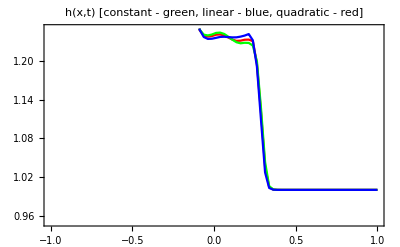
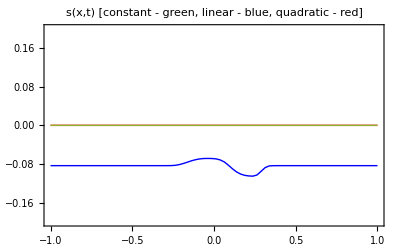
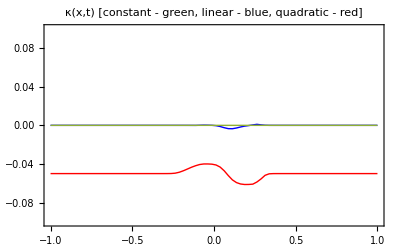
-Graphics- | 
 | 
-Graphics- | -Graphics-

```mathematica
p={{-0.4,0.25},{0.0,0.25},{0.4,0.25}};
Grid[{{
Plot[{hQ[x],hL[x],hSW[x]},{x,x1,x2},
PlotRange->{{x1,x2},{0.95,1.25}},PlotStyle->color⟦1;;3⟧,PlotLabel->"h(x,t) [constant - green, linear - blue, quadratic - red]",
ImageSize->iSize,Frame->True]
},{
LocatorPane[Dynamic[p],
Dynamic[
Plot[{uMeanQ[x],uMeanL[x],uMeanSW[x]},{x,x1,x2},PlotRange->{{x1,x2},{0.05,0.45}},PlotStyle->color⟦1;;3⟧,
PlotLabel->"u_m(x,t) [constant - green, linear - blue, quadratic - red]",ImageSize->iSize,Frame->True,
Epilog->{PointSize[0.03],color⟦1⟧,Point[{p⟦1,1⟧,uMeanQ[p⟦1,1⟧]}],color⟦2⟧,Point[{p⟦2,1⟧,uMeanL[p⟦2,1⟧]}],color⟦3⟧,Point[{p⟦3,1⟧,uMeanSW[p⟦3,1⟧]}]}]],Appearance->None],
Dynamic[
ParametricPlot[Evaluate[{{uFullQ[p⟦1,1⟧,y],y},{uFullL[p⟦2,1⟧,y],y},{uFullSW[p⟦3,1⟧,y],y}}],{y,y1,y2},AspectRatio->0.5,PlotRange->{{-0.15,0.65},{0,1}},PlotStyle->color⟦1;;3⟧,
PlotLabel->"velocity profiles [intial velocity - thin]",Frame->True,ImageSize->1.2iSize]]
},{
Plot[{sQ[x],sL[x],sSW[x]},{x,x1,x2},
PlotRange->{{x1,x2},{-0.2,0.2}},PlotStyle->{{Thick,Red},{Thick,Blue},Thin},PlotLabel->"s(x,t) [constant - green, linear - blue, quadratic - red]",
ImageSize->iSize,Frame->True],
Plot[{κQ[x],κL[x],κSW[x]},{x,x1,x2},
PlotRange->{{x1,x2},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},Thin},PlotLabel->"κ(x,t) [constant - green, linear - blue, quadratic - red]",
ImageSize->iSize,Frame->True]
}},
Alignment->{{Right,Left},{Right,Left},{Right,Left}}
]
```

### "Open/Close" Depth-Projected Shallow Flow (friction, linear / moderate quadratic /small quadratic profiles)

```mathematica
u0[x_,y_]=0.5y;
```

```mathematica
(*χ=10^6;
R=0.01;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=1;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
```

```mathematica
(*χ=10^6;
R=0.1;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=2;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
```

```mathematica
χ=0.1;
R=0.1;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=1;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

$Aborted

{{1.0375,1.3,1/20 (1. u0[1.0375,0.025]+1. u0[1.0375,0.075]+17+1. u0[1.0375,0.975]),0.0475 u0[1.0375,0.025]+0.0425 u0[1.0375,0.075]+0.0375 u0[1.0375,0.125]+0.0325 u0[1.0375,0.175]+26,0.04275 u0[1.0375,0.025]+0.02925 u0[1.0375,0.075]+0.01725 u0[1.0375,0.125]+25+0.00675 u0[1.0375,0.825]+0.01725 u0[1.0375,0.875]+0.02925 u0[1.0375,0.925]+0.04275 u0[1.0375,0.975]},38,{3.9625,3,1}}
 |  |  |  |

```mathematica
χ=0.1;
R=0.1;
u0[x_,y_]=1.5y(1-y);
FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=2;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]],Map[Mean,Vraw]},{i,1,nx}]
```

{{-0.9875,1.5,0.243897,-0.00533758,-0.0371752},{-0.9625,1.5,0.243897,-0.00533758,-0.0371752},{-0.9375,1.5,0.243897,-0.00533758,-0.0371752},{-0.9125,1.5,0.243897,-0.00533758,-0.0371752},{-0.8875,1.5,0.243897,-0.00533758,-0.0371752},{-0.8625,1.5,0.243897,-0.00533758,-0.0371752},{-0.8375,1.5,0.243897,-0.00533758,-0.0371752},{-0.8125,1.5,0.243897,-0.00533758,-0.0371752},{-0.7875,1.5,0.243897,-0.00533758,-0.0371752},{-0.7625,1.5,0.243897,-0.00533758,-0.0371752},{-0.7375,1.5,0.243897,-0.00533758,-0.0371752},{-0.7125,1.5,0.243897,-0.00533758,-0.0371752},{-0.6875,1.5,0.243897,-0.00533758,-0.0371752},{-0.6625,1.5,0.243897,-0.00533758,-0.0371752},{-0.6375,1.5,0.243897,-0.00533758,-0.0371752},{-0.6125,1.5,0.243897,-0.00533758,-0.0371752},{-0.5875,1.5,0.243897,-0.00533758,-0.0371752},{-0.5625,1.5,0.243897,-0.00533758,-0.0371752},{-0.5375,1.5,0.243897,-0.00533758,-0.0371752},{-0.5125,1.5,0.243897,-0.00533758,-0.0371752},{-0.4875,1.5,0.243897,-0.00533758,-0.0371752},{-0.4625,1.5,0.243897,-0.00533758,-0.0371752},{-0.4375,1.5,0.243897,-0.00533758,-0.0371752},{-0.4125,1.5,0.243897,-0.00533758,-0.0371752},{-0.3875,1.5,0.243897,-0.00533758,-0.0371752},{-0.3625,1.5,0.243898,-0.00533759,-0.0371752},{-0.3375,1.49999,0.243904,-0.00533763,-0.0371751},{-0.3125,1.49994,0.243943,-0.00533788,-0.0371743},{-0.2875,1.49965,0.244185,-0.00533943,-0.0371693},{-0.2625,1.49794,0.245578,-0.00534812,-0.0371398},{-0.2375,1.4889,0.252942,-0.00538935,-0.0369745},{-0.2125,1.46424,0.273231,-0.00557941,-0.0365424},{-0.1875,1.42477,0.305814,-0.0061139,-0.0359749},{-0.1625,1.37644,0.346155,-0.0070714,-0.035418},{-0.1375,1.32643,0.388366,-0.00838085,-0.0349768},{-0.1125,1.28343,0.425195,-0.0100198,-0.0349061},{-0.0875,1.25454,0.449101,-0.0123066,-0.0356147},{-0.0625,1.24389,0.458145,-0.0150168,-0.0362005},{-0.0375,1.24126,0.459327,-0.0175925,-0.0363987},{-0.0125,1.24046,0.458302,-0.0198316,-0.0369532},{0.0125,1.23983,0.45745,-0.0212825,-0.0376798},{0.0375,1.23871,0.457536,-0.022057,-0.0385413},{0.0625,1.23741,0.458432,-0.0219361,-0.0395859},{0.0875,1.23571,0.458708,-0.0206336,-0.0410717},{0.1125,1.23361,0.457946,-0.0188236,-0.0426304},{0.1375,1.23205,0.457347,-0.0173956,-0.0435714},{0.1625,1.23183,0.457976,-0.0163321,-0.0435221},{0.1875,1.23226,0.45914,-0.0154093,-0.0428099},{0.2125,1.23377,0.459542,-0.0148897,-0.0416525},{0.2375,1.22819,0.454953,-0.0143523,-0.039211},{0.2625,1.18834,0.419307,-0.0131491,-0.0353977},{0.2875,1.10756,0.342962,-0.0117993,-0.0317591},{0.3125,1.02826,0.265516,-0.0106252,-0.0285811},{0.3375,1.00328,0.240528,-0.0102607,-0.0276129},{0.3625,1.00034,0.237571,-0.0102162,-0.0274867},{0.3875,1.00003,0.237269,-0.0102116,-0.0274738},{0.4125,1.,0.237238,-0.0102112,-0.0274724},{0.4375,1.,0.237235,-0.0102111,-0.0274723},{0.4625,1.,0.237234,-0.0102111,-0.0274723},{0.4875,1.,0.237234,-0.0102111,-0.0274723},{0.5125,1.,0.237234,-0.0102111,-0.0274723},{0.5375,1.,0.237234,-0.0102111,-0.0274723},{0.5625,1.,0.237234,-0.0102111,-0.0274723},{0.5875,1.,0.237234,-0.0102111,-0.0274723},{0.6125,1.,0.237234,-0.0102111,-0.0274723},{0.6375,1.,0.237234,-0.0102111,-0.0274723},{0.6625,1.,0.237234,-0.0102111,-0.0274723},{0.6875,1.,0.237234,-0.0102111,-0.0274723},{0.7125,1.,0.237234,-0.0102111,-0.0274723},{0.7375,1.,0.237234,-0.0102111,-0.0274723},{0.7625,1.,0.237234,-0.0102111,-0.0274723},{0.7875,1.,0.237234,-0.0102111,-0.0274723},{0.8125,1.,0.237234,-0.0102111,-0.0274723},{0.8375,1.,0.237234,-0.0102111,-0.0274723},{0.8625,1.,0.237234,-0.0102111,-0.0274723},{0.8875,1.,0.237234,-0.0102111,-0.0274723},{0.9125,1.,0.237234,-0.0102111,-0.0274723},{0.9375,1.,0.237234,-0.0102111,-0.0274723},{0.9625,1.,0.237234,-0.0102111,-0.0274723},{0.9875,1.,0.237234,-0.0102111,-0.0274723}}

```mathematica
(*u0[x_,y_]=0.15 +0.6y(1-y);*)
u0[x_,y_]=0.25-2.5*y+7.5*y^2-5*y^3;
v0[x_,y_]=0.0;
(*u0[x_,y_]=0.0;*)
(*v0[x_,y_]=0.5;*)

χ=0.1;
R=0.1;
FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=3;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]],Map[Mean,Vraw][[i]]},{i,1,nx}] //MatrixForm
```

(10.0125 | 4.98766 | 0.247315 | -0.0855827 | -0.0019846 | 0.
10.0375 | 4.98768 | 0.247306 | -0.0855832 | -0.00198476 | 0.
10.0625 | 4.98769 | 0.247301 | -0.0855829 | -0.00198517 | 0.
10.0875 | 4.98771 | 0.247296 | -0.0855827 | -0.00198552 | 0.
10.1125 | 4.98773 | 0.247293 | -0.0855824 | -0.00198583 | 0.
10.1375 | 4.98775 | 0.24729 | -0.0855823 | -0.00198614 | 0.
10.1625 | 4.98778 | 0.247287 | -0.0855821 | -0.00198643 | 0.
10.1875 | 4.9878 | 0.247286 | -0.085582 | -0.00198675 | 0.
10.2125 | 4.98783 | 0.247285 | -0.0855819 | -0.00198712 | 0.
10.2375 | 4.98786 | 0.247285 | -0.0855819 | -0.00198748 | 0.
10.2625 | 4.98788 | 0.247286 | -0.0855819 | -0.00198783 | 0.
10.2875 | 4.98791 | 0.247286 | -0.0855819 | -0.00198817 | 0.
10.3125 | 4.98794 | 0.247288 | -0.0855819 | -0.00198852 | 0.
10.3375 | 4.98797 | 0.247289 | -0.0855819 | -0.00198887 | 0.
10.3625 | 4.988 | 0.24729 | -0.0855819 | -0.00198921 | 0.
10.3875 | 4.98803 | 0.247291 | -0.0855819 | -0.00198956 | 0.
10.4125 | 4.98806 | 0.247292 | -0.0855819 | -0.0019899 | 0.
10.4375 | 4.98809 | 0.247293 | -0.0855819 | -0.00199024 | 0.
10.4625 | 4.98812 | 0.247293 | -0.0855819 | -0.00199058 | 0.
10.4875 | 4.98814 | 0.247294 | -0.0855819 | -0.00199092 | 0.
10.5125 | 4.98817 | 0.247295 | -0.0855819 | -0.00199125 | 0.
10.5375 | 4.9882 | 0.247296 | -0.0855818 | -0.00199159 | 0.
10.5625 | 4.98823 | 0.247297 | -0.0855818 | -0.00199192 | 0.
10.5875 | 4.98826 | 0.247298 | -0.0855818 | -0.00199225 | 0.
10.6125 | 4.98828 | 0.247299 | -0.0855818 | -0.00199258 | 0.
10.6375 | 4.98831 | 0.2473 | -0.0855818 | -0.00199291 | 0.
10.6625 | 4.98834 | 0.247301 | -0.0855818 | -0.00199324 | 0.
10.6875 | 4.98837 | 0.247302 | -0.0855818 | -0.00199356 | 0.
10.7125 | 4.98839 | 0.247303 | -0.0855818 | -0.00199388 | 0.
10.7375 | 4.98842 | 0.247304 | -0.0855818 | -0.00199421 | 0.
10.7625 | 4.98845 | 0.247305 | -0.0855818 | -0.00199453 | 0.
10.7875 | 4.98847 | 0.247305 | -0.0855818 | -0.00199485 | 0.
10.8125 | 4.9885 | 0.247306 | -0.0855818 | -0.00199516 | 0.
10.8375 | 4.98853 | 0.247307 | -0.0855818 | -0.00199548 | 0.
10.8625 | 4.98855 | 0.247308 | -0.0855818 | -0.00199579 | 0.
10.8875 | 4.98858 | 0.247309 | -0.0855818 | -0.00199611 | 0.
10.9125 | 4.98861 | 0.24731 | -0.0855818 | -0.00199642 | 0.
10.9375 | 4.98863 | 0.247311 | -0.0855818 | -0.00199673 | 0.
10.9625 | 4.98866 | 0.247312 | -0.0855818 | -0.00199704 | 0.
10.9875 | 4.98868 | 0.247312 | -0.0855818 | -0.00199734 | 0.
11.0125 | 4.98871 | 0.247313 | -0.0855818 | -0.00199765 | 0.
11.0375 | 4.98873 | 0.247314 | -0.0855818 | -0.00199795 | 0.
11.0625 | 4.98876 | 0.247315 | -0.0855818 | -0.00199826 | 0.
11.0875 | 4.98879 | 0.247316 | -0.0855818 | -0.00199856 | 0.
11.1125 | 4.98881 | 0.247317 | -0.0855818 | -0.00199886 | 0.
11.1375 | 4.98884 | 0.247317 | -0.0855818 | -0.00199916 | 0.
11.1625 | 4.98886 | 0.247318 | -0.0855818 | -0.00199946 | 0.
11.1875 | 4.98889 | 0.247319 | -0.0855818 | -0.00199975 | 0.
11.2125 | 4.98891 | 0.24732 | -0.0855818 | -0.00200005 | 0.
11.2375 | 4.98894 | 0.247321 | -0.0855818 | -0.00200034 | 0.
11.2625 | 4.98896 | 0.247322 | -0.0855818 | -0.00200063 | 0.
11.2875 | 4.98898 | 0.247322 | -0.0855818 | -0.00200092 | 0.
11.3125 | 4.98901 | 0.247323 | -0.0855818 | -0.00200121 | 0.
11.3375 | 4.98903 | 0.247324 | -0.0855818 | -0.0020015 | 0.
11.3625 | 4.98906 | 0.247325 | -0.0855818 | -0.00200179 | 0.
11.3875 | 4.98908 | 0.247326 | -0.0855818 | -0.00200208 | 0.
11.4125 | 4.9891 | 0.247326 | -0.0855818 | -0.00200236 | 0.
11.4375 | 4.98913 | 0.247327 | -0.0855818 | -0.00200264 | 0.
11.4625 | 4.98915 | 0.247328 | -0.0855818 | -0.00200293 | 0.
11.4875 | 4.98918 | 0.247329 | -0.0855818 | -0.00200321 | 0.
11.5125 | 4.9892 | 0.247329 | -0.0855818 | -0.00200349 | 0.
11.5375 | 4.98922 | 0.24733 | -0.0855818 | -0.00200377 | 0.
11.5625 | 4.98925 | 0.247331 | -0.0855818 | -0.00200404 | 0.
11.5875 | 4.98927 | 0.247332 | -0.0855818 | -0.00200432 | 0.
11.6125 | 4.98929 | 0.247333 | -0.0855818 | -0.00200459 | 0.
11.6375 | 4.98932 | 0.247333 | -0.0855818 | -0.00200487 | 0.
11.6625 | 4.98934 | 0.247334 | -0.0855818 | -0.00200514 | 0.
11.6875 | 4.98936 | 0.247335 | -0.0855818 | -0.00200541 | 0.
11.7125 | 4.98938 | 0.247335 | -0.0855818 | -0.00200568 | 0.
11.7375 | 4.98941 | 0.247336 | -0.0855818 | -0.00200595 | 0.
11.7625 | 4.98943 | 0.247337 | -0.0855818 | -0.00200622 | 0.
11.7875 | 4.98945 | 0.247338 | -0.0855818 | -0.00200649 | 0.
11.8125 | 4.98947 | 0.247338 | -0.0855818 | -0.00200675 | 0.
11.8375 | 4.9895 | 0.247339 | -0.0855817 | -0.00200702 | 0.
11.8625 | 4.98952 | 0.24734 | -0.0855817 | -0.00200728 | 0.
11.8875 | 4.98954 | 0.247341 | -0.0855817 | -0.00200754 | 0.
11.9125 | 4.98956 | 0.247341 | -0.0855817 | -0.0020078 | 0.
11.9375 | 4.98958 | 0.247342 | -0.0855817 | -0.00200806 | 0.
11.9625 | 4.98961 | 0.247343 | -0.0855817 | -0.00200832 | 0.
11.9875 | 4.98963 | 0.247343 | -0.0855817 | -0.00200858 | 0.
12.0125 | 4.98965 | 0.247344 | -0.0855817 | -0.00200884 | 0.
12.0375 | 4.98967 | 0.247345 | -0.0855817 | -0.00200909 | 0.
12.0625 | 4.98969 | 0.247345 | -0.0855817 | -0.00200935 | 0.
12.0875 | 4.98971 | 0.247346 | -0.0855817 | -0.0020096 | 0.
12.1125 | 4.98973 | 0.247347 | -0.0855817 | -0.00200985 | 0.
12.1375 | 4.98976 | 0.247348 | -0.0855817 | -0.00201011 | 0.
12.1625 | 4.98978 | 0.247348 | -0.0855817 | -0.00201036 | 0.
12.1875 | 4.9898 | 0.247349 | -0.0855817 | -0.00201061 | 0.
12.2125 | 4.98982 | 0.24735 | -0.0855817 | -0.00201086 | 0.
12.2375 | 4.98984 | 0.24735 | -0.0855817 | -0.0020111 | 0.
12.2625 | 4.98986 | 0.247351 | -0.0855817 | -0.00201135 | 0.
12.2875 | 4.98988 | 0.247352 | -0.0855817 | -0.00201159 | 0.
12.3125 | 4.9899 | 0.247352 | -0.0855817 | -0.00201184 | 0.
12.3375 | 4.98992 | 0.247353 | -0.0855817 | -0.00201208 | 0.
12.3625 | 4.98994 | 0.247354 | -0.0855817 | -0.00201232 | 0.
12.3875 | 4.98996 | 0.247354 | -0.0855817 | -0.00201257 | 0.
12.4125 | 4.98998 | 0.247355 | -0.0855817 | -0.00201281 | 0.
12.4375 | 4.99 | 0.247356 | -0.0855817 | -0.00201305 | 0.
12.4625 | 4.99002 | 0.247356 | -0.0855817 | -0.00201328 | 0.
12.4875 | 4.99004 | 0.247357 | -0.0855817 | -0.00201352 | 0.
12.5125 | 4.99006 | 0.247357 | -0.0855817 | -0.00201376 | 0.
12.5375 | 4.99008 | 0.247358 | -0.0855817 | -0.00201399 | 0.
12.5625 | 4.9901 | 0.247359 | -0.0855817 | -0.00201423 | 0.
12.5875 | 4.99012 | 0.247359 | -0.0855817 | -0.00201446 | 0.
12.6125 | 4.99014 | 0.24736 | -0.0855817 | -0.0020147 | 0.
12.6375 | 4.99016 | 0.247361 | -0.0855817 | -0.00201493 | 0.
12.6625 | 4.99018 | 0.247361 | -0.0855817 | -0.00201516 | 0.
12.6875 | 4.9902 | 0.247362 | -0.0855817 | -0.00201539 | 0.
12.7125 | 4.99022 | 0.247362 | -0.0855817 | -0.00201562 | 0.
12.7375 | 4.99024 | 0.247363 | -0.0855817 | -0.00201585 | 0.
12.7625 | 4.99026 | 0.247364 | -0.0855817 | -0.00201607 | 0.
12.7875 | 4.99028 | 0.247364 | -0.0855817 | -0.0020163 | 0.
12.8125 | 4.9903 | 0.247365 | -0.0855817 | -0.00201653 | 0.
12.8375 | 4.99031 | 0.247365 | -0.0855817 | -0.00201675 | 0.
12.8625 | 4.99033 | 0.247366 | -0.0855817 | -0.00201698 | 0.
12.8875 | 4.99035 | 0.247367 | -0.0855817 | -0.0020172 | 0.
12.9125 | 4.99037 | 0.247367 | -0.0855817 | -0.00201742 | 0.
12.9375 | 4.99039 | 0.247368 | -0.0855817 | -0.00201764 | 0.
12.9625 | 4.99041 | 0.247368 | -0.0855817 | -0.00201786 | 0.
12.9875 | 4.99043 | 0.247369 | -0.0855817 | -0.00201808 | 0.
13.0125 | 4.99044 | 0.24737 | -0.0855817 | -0.0020183 | 0.
13.0375 | 4.99046 | 0.24737 | -0.0855817 | -0.00201852 | 0.
13.0625 | 4.99048 | 0.247371 | -0.0855817 | -0.00201874 | 0.
13.0875 | 4.9905 | 0.247371 | -0.0855817 | -0.00201895 | 0.
13.1125 | 4.99052 | 0.247372 | -0.0855817 | -0.00201917 | 0.
13.1375 | 4.99054 | 0.247372 | -0.0855817 | -0.00201938 | 0.
13.1625 | 4.99055 | 0.247373 | -0.0855817 | -0.0020196 | 0.
13.1875 | 4.99057 | 0.247374 | -0.0855817 | -0.00201981 | 0.
13.2125 | 4.99059 | 0.247374 | -0.0855817 | -0.00202002 | 0.
13.2375 | 4.99061 | 0.247375 | -0.0855817 | -0.00202023 | 0.
13.2625 | 4.99062 | 0.247375 | -0.0855817 | -0.00202044 | 0.
13.2875 | 4.99064 | 0.247376 | -0.0855817 | -0.00202065 | 0.
13.3125 | 4.99066 | 0.247376 | -0.0855816 | -0.00202086 | 0.
13.3375 | 4.99068 | 0.247377 | -0.0855816 | -0.00202107 | 0.
13.3625 | 4.99069 | 0.247378 | -0.0855816 | -0.00202128 | 0.
13.3875 | 4.99071 | 0.247378 | -0.0855816 | -0.00202148 | 0.
13.4125 | 4.99073 | 0.247379 | -0.0855816 | -0.00202169 | 0.
13.4375 | 4.99075 | 0.247379 | -0.0855816 | -0.0020219 | 0.
13.4625 | 4.99076 | 0.24738 | -0.0855816 | -0.0020221 | 0.
13.4875 | 4.99078 | 0.24738 | -0.0855816 | -0.0020223 | 0.
13.5125 | 4.9908 | 0.247381 | -0.0855816 | -0.00202251 | 0.
13.5375 | 4.99082 | 0.247381 | -0.0855816 | -0.00202271 | 0.
13.5625 | 4.99083 | 0.247381 | -0.0855817 | -0.00202291 | 0.
13.5875 | 4.99085 | 0.247381 | -0.0855816 | -0.00202308 | 0.
13.6125 | 4.99087 | 0.247383 | -0.0855815 | -0.00202328 | 0.
13.6375 | 4.99087 | 0.24739 | -0.0855814 | -0.00202351 | 0.
13.6625 | 4.99084 | 0.247411 | -0.0855807 | -0.0020238 | 0.
13.6875 | 4.99056 | 0.247542 | -0.0855765 | -0.00202472 | 0.
13.7125 | 4.98882 | 0.248334 | -0.0855502 | -0.00202942 | 0.
13.7375 | 4.97886 | 0.252831 | -0.0853975 | -0.00205557 | 0.
13.7625 | 4.9273 | 0.276081 | -0.0845759 | -0.00219417 | 0.
13.7875 | 4.79901 | 0.334848 | -0.0824962 | -0.00256914 | 0.
13.8125 | 4.60274 | 0.425724 | -0.0794258 | -0.00319727 | 0.
13.8375 | 4.36387 | 0.538899 | -0.0757966 | -0.00404822 | 0.
13.8625 | 4.10465 | 0.665211 | -0.0720278 | -0.00509688 | 0.
13.8875 | 3.8385 | 0.798462 | -0.0683717 | -0.0063297 | 0.
13.9125 | 3.57336 | 0.935732 | -0.0650083 | -0.00771008 | 0.
13.9375 | 3.31412 | 1.07545 | -0.0622875 | -0.00916698 | 0.
13.9625 | 3.06514 | 1.21372 | -0.060578 | -0.011129 | 0.
13.9875 | 2.83292 | 1.34427 | -0.0584996 | -0.0139364 | 0.
14.0125 | 2.64619 | 1.45871 | -0.0561333 | -0.0166074 | 0.
14.0375 | 2.53118 | 1.52874 | -0.0577187 | -0.0188712 | 0.
14.0625 | 2.497 | 1.5458 | -0.0625615 | -0.0217357 | 0.
14.0875 | 2.49952 | 1.53811 | -0.0695888 | -0.0243884 | 0.
14.1125 | 2.51452 | 1.51664 | -0.0852715 | -0.0256374 | 0.
14.1375 | 2.529 | 1.49812 | -0.120359 | -0.0255134 | 0.
14.1625 | 2.53255 | 1.48917 | -0.169019 | -0.03328 | 0.
14.1875 | 2.44978 | 1.48578 | -0.211166 | -0.0491108 | 0.
14.2125 | 2.2423 | 1.47155 | -0.248082 | -0.0773843 | 0.
14.2375 | 1.71843 | 1.09276 | -0.203484 | -0.085138 | 0.
14.2625 | 1.12105 | 0.399576 | -0.105623 | -0.0200436 | 0.
14.2875 | 1.00484 | 0.25028 | -0.0850367 | -0.0041894 | 0.
14.3125 | 0.998586 | 0.243291 | -0.0841494 | -0.00374149 | 0.
14.3375 | 0.998301 | 0.242982 | -0.084113 | -0.00372913 | 0.
14.3625 | 0.99829 | 0.242968 | -0.0841114 | -0.0037288 | 0.
14.3875 | 0.998292 | 0.242967 | -0.0841113 | -0.00372888 | 0.
14.4125 | 0.998295 | 0.242968 | -0.0841113 | -0.00372902 | 0.
14.4375 | 0.998298 | 0.242968 | -0.0841113 | -0.00372915 | 0.
14.4625 | 0.998301 | 0.242968 | -0.0841113 | -0.00372927 | 0.
14.4875 | 0.998304 | 0.242969 | -0.0841113 | -0.00372939 | 0.
14.5125 | 0.998307 | 0.242969 | -0.0841114 | -0.00372951 | 0.
14.5375 | 0.99831 | 0.242969 | -0.0841114 | -0.00372964 | 0.
14.5625 | 0.998313 | 0.24297 | -0.0841114 | -0.00372976 | 0.
14.5875 | 0.998316 | 0.24297 | -0.0841114 | -0.00372988 | 0.
14.6125 | 0.998319 | 0.24297 | -0.0841114 | -0.00373 | 0.
14.6375 | 0.998322 | 0.242971 | -0.0841114 | -0.00373012 | 0.
14.6625 | 0.998324 | 0.242971 | -0.0841114 | -0.00373024 | 0.
14.6875 | 0.998327 | 0.242971 | -0.0841114 | -0.00373036 | 0.
14.7125 | 0.99833 | 0.242972 | -0.0841114 | -0.00373048 | 0.
14.7375 | 0.998333 | 0.242972 | -0.0841114 | -0.0037306 | 0.
14.7625 | 0.998336 | 0.242972 | -0.0841115 | -0.00373071 | 0.
14.7875 | 0.998339 | 0.242973 | -0.0841115 | -0.00373083 | 0.
14.8125 | 0.998341 | 0.242973 | -0.0841115 | -0.00373095 | 0.
14.8375 | 0.998344 | 0.242973 | -0.0841115 | -0.00373107 | 0.
14.8625 | 0.998347 | 0.242974 | -0.0841115 | -0.00373118 | 0.
14.8875 | 0.99835 | 0.242974 | -0.0841115 | -0.0037313 | 0.
14.9125 | 0.998353 | 0.242974 | -0.0841115 | -0.00373141 | 0.
14.9375 | 0.998355 | 0.242975 | -0.0841115 | -0.00373153 | 0.
14.9625 | 0.998358 | 0.242975 | -0.0841115 | -0.00373165 | 0.
14.9875 | 0.998361 | 0.242975 | -0.0841115 | -0.00373176 | 0.
15.0125 | 0.998363 | 0.242975 | -0.0841115 | -0.00373187 | 0.
15.0375 | 0.998366 | 0.242976 | -0.0841116 | -0.00373199 | 0.
15.0625 | 0.998369 | 0.242976 | -0.0841116 | -0.0037321 | 0.
15.0875 | 0.998372 | 0.242976 | -0.0841116 | -0.00373221 | 0.
15.1125 | 0.998374 | 0.242977 | -0.0841116 | -0.00373233 | 0.
15.1375 | 0.998377 | 0.242977 | -0.0841116 | -0.00373244 | 0.
15.1625 | 0.99838 | 0.242977 | -0.0841116 | -0.00373255 | 0.
15.1875 | 0.998382 | 0.242978 | -0.0841116 | -0.00373266 | 0.
15.2125 | 0.998385 | 0.242978 | -0.0841116 | -0.00373277 | 0.
15.2375 | 0.998388 | 0.242978 | -0.0841116 | -0.00373289 | 0.
15.2625 | 0.99839 | 0.242979 | -0.0841116 | -0.003733 | 0.
15.2875 | 0.998393 | 0.242979 | -0.0841117 | -0.00373311 | 0.
15.3125 | 0.998396 | 0.242979 | -0.0841117 | -0.00373322 | 0.
15.3375 | 0.998398 | 0.242979 | -0.0841117 | -0.00373333 | 0.
15.3625 | 0.998401 | 0.24298 | -0.0841117 | -0.00373343 | 0.
15.3875 | 0.998403 | 0.24298 | -0.0841117 | -0.00373354 | 0.
15.4125 | 0.998406 | 0.24298 | -0.0841117 | -0.00373365 | 0.
15.4375 | 0.998409 | 0.242981 | -0.0841117 | -0.00373376 | 0.
15.4625 | 0.998411 | 0.242981 | -0.0841117 | -0.00373387 | 0.
15.4875 | 0.998414 | 0.242981 | -0.0841117 | -0.00373398 | 0.
15.5125 | 0.998416 | 0.242981 | -0.0841117 | -0.00373408 | 0.
15.5375 | 0.998419 | 0.242982 | -0.0841117 | -0.00373419 | 0.
15.5625 | 0.998421 | 0.242982 | -0.0841117 | -0.0037343 | 0.
15.5875 | 0.998424 | 0.242982 | -0.0841118 | -0.0037344 | 0.
15.6125 | 0.998426 | 0.242983 | -0.0841118 | -0.00373451 | 0.
15.6375 | 0.998429 | 0.242983 | -0.0841118 | -0.00373461 | 0.
15.6625 | 0.998431 | 0.242983 | -0.0841118 | -0.00373472 | 0.
15.6875 | 0.998434 | 0.242983 | -0.0841118 | -0.00373482 | 0.
15.7125 | 0.998436 | 0.242984 | -0.0841118 | -0.00373493 | 0.
15.7375 | 0.998439 | 0.242984 | -0.0841118 | -0.00373503 | 0.
15.7625 | 0.998441 | 0.242984 | -0.0841118 | -0.00373513 | 0.
15.7875 | 0.998444 | 0.242985 | -0.0841118 | -0.00373524 | 0.
15.8125 | 0.998446 | 0.242985 | -0.0841118 | -0.00373534 | 0.
15.8375 | 0.998449 | 0.242985 | -0.0841118 | -0.00373544 | 0.
15.8625 | 0.998451 | 0.242985 | -0.0841119 | -0.00373554 | 0.
15.8875 | 0.998454 | 0.242986 | -0.0841119 | -0.00373565 | 0.
15.9125 | 0.998456 | 0.242986 | -0.0841119 | -0.00373575 | 0.
15.9375 | 0.998458 | 0.242986 | -0.0841119 | -0.00373585 | 0.
15.9625 | 0.998461 | 0.242987 | -0.0841119 | -0.00373595 | 0.
15.9875 | 0.998463 | 0.242987 | -0.0841119 | -0.00373605 | 0.
16.0125 | 0.998466 | 0.242987 | -0.0841119 | -0.00373615 | 0.
16.0375 | 0.998468 | 0.242987 | -0.0841119 | -0.00373625 | 0.
16.0625 | 0.99847 | 0.242988 | -0.0841119 | -0.00373635 | 0.
16.0875 | 0.998473 | 0.242988 | -0.0841119 | -0.00373645 | 0.
16.1125 | 0.998475 | 0.242988 | -0.0841119 | -0.00373655 | 0.
16.1375 | 0.998478 | 0.242988 | -0.0841119 | -0.00373665 | 0.
16.1625 | 0.99848 | 0.242989 | -0.0841119 | -0.00373675 | 0.
16.1875 | 0.998482 | 0.242989 | -0.084112 | -0.00373685 | 0.
16.2125 | 0.998485 | 0.242989 | -0.084112 | -0.00373694 | 0.
16.2375 | 0.998487 | 0.242989 | -0.084112 | -0.00373704 | 0.
16.2625 | 0.998489 | 0.24299 | -0.084112 | -0.00373714 | 0.
16.2875 | 0.998492 | 0.24299 | -0.084112 | -0.00373724 | 0.
16.3125 | 0.998494 | 0.24299 | -0.084112 | -0.00373733 | 0.
16.3375 | 0.998496 | 0.24299 | -0.084112 | -0.00373743 | 0.
16.3625 | 0.998499 | 0.242991 | -0.084112 | -0.00373753 | 0.
16.3875 | 0.998501 | 0.242991 | -0.084112 | -0.00373762 | 0.
16.4125 | 0.998503 | 0.242991 | -0.084112 | -0.00373772 | 0.
16.4375 | 0.998505 | 0.242992 | -0.084112 | -0.00373781 | 0.
16.4625 | 0.998508 | 0.242992 | -0.084112 | -0.00373791 | 0.
16.4875 | 0.99851 | 0.242992 | -0.0841121 | -0.003738 | 0.
16.5125 | 0.998512 | 0.242992 | -0.0841121 | -0.0037381 | 0.
16.5375 | 0.998514 | 0.242993 | -0.0841121 | -0.00373819 | 0.
16.5625 | 0.998517 | 0.242993 | -0.0841121 | -0.00373828 | 0.
16.5875 | 0.998519 | 0.242993 | -0.0841121 | -0.00373838 | 0.
16.6125 | 0.998521 | 0.242993 | -0.0841121 | -0.00373847 | 0.
16.6375 | 0.998523 | 0.242994 | -0.0841121 | -0.00373856 | 0.
16.6625 | 0.998526 | 0.242994 | -0.0841121 | -0.00373866 | 0.
16.6875 | 0.998528 | 0.242994 | -0.0841121 | -0.00373875 | 0.
16.7125 | 0.99853 | 0.242994 | -0.0841121 | -0.00373884 | 0.
16.7375 | 0.998532 | 0.242995 | -0.0841121 | -0.00373893 | 0.
16.7625 | 0.998534 | 0.242995 | -0.0841121 | -0.00373903 | 0.
16.7875 | 0.998537 | 0.242995 | -0.0841121 | -0.00373912 | 0.
16.8125 | 0.998539 | 0.242995 | -0.0841121 | -0.00373921 | 0.
16.8375 | 0.998541 | 0.242996 | -0.0841122 | -0.0037393 | 0.
16.8625 | 0.998543 | 0.242996 | -0.0841122 | -0.00373939 | 0.
16.8875 | 0.998545 | 0.242996 | -0.0841122 | -0.00373948 | 0.
16.9125 | 0.998547 | 0.242996 | -0.0841122 | -0.00373957 | 0.
16.9375 | 0.998549 | 0.242996 | -0.0841122 | -0.00373966 | 0.
16.9625 | 0.998552 | 0.242997 | -0.0841122 | -0.00373975 | 0.
16.9875 | 0.998554 | 0.242997 | -0.0841122 | -0.00373984 | 0.
17.0125 | 0.998556 | 0.242997 | -0.0841122 | -0.00373993 | 0.
17.0375 | 0.998558 | 0.242997 | -0.0841122 | -0.00374001 | 0.
17.0625 | 0.99856 | 0.242998 | -0.0841122 | -0.0037401 | 0.
17.0875 | 0.998562 | 0.242998 | -0.0841122 | -0.00374019 | 0.
17.1125 | 0.998564 | 0.242998 | -0.0841122 | -0.00374028 | 0.
17.1375 | 0.998566 | 0.242998 | -0.0841122 | -0.00374037 | 0.
17.1625 | 0.998568 | 0.242999 | -0.0841123 | -0.00374045 | 0.
17.1875 | 0.998571 | 0.242999 | -0.0841123 | -0.00374054 | 0.
17.2125 | 0.998573 | 0.242999 | -0.0841123 | -0.00374063 | 0.
17.2375 | 0.998575 | 0.242999 | -0.0841123 | -0.00374072 | 0.
17.2625 | 0.998577 | 0.243 | -0.0841123 | -0.0037408 | 0.
17.2875 | 0.998579 | 0.243 | -0.0841123 | -0.00374089 | 0.
17.3125 | 0.998581 | 0.243 | -0.0841123 | -0.00374097 | 0.
17.3375 | 0.998583 | 0.243 | -0.0841123 | -0.00374106 | 0.
17.3625 | 0.998585 | 0.243 | -0.0841123 | -0.00374114 | 0.
17.3875 | 0.998587 | 0.243001 | -0.0841123 | -0.00374123 | 0.
17.4125 | 0.998589 | 0.243001 | -0.0841123 | -0.00374131 | 0.
17.4375 | 0.998591 | 0.243001 | -0.0841123 | -0.0037414 | 0.
17.4625 | 0.998593 | 0.243001 | -0.0841123 | -0.00374148 | 0.
17.4875 | 0.998595 | 0.243002 | -0.0841123 | -0.00374157 | 0.
17.5125 | 0.998597 | 0.243002 | -0.0841123 | -0.00374165 | 0.
17.5375 | 0.998599 | 0.243002 | -0.0841124 | -0.00374174 | 0.
17.5625 | 0.998601 | 0.243002 | -0.0841124 | -0.00374182 | 0.
17.5875 | 0.998603 | 0.243003 | -0.0841124 | -0.0037419 | 0.
17.6125 | 0.998605 | 0.243003 | -0.0841124 | -0.00374198 | 0.
17.6375 | 0.998607 | 0.243003 | -0.0841124 | -0.00374207 | 0.
17.6625 | 0.998609 | 0.243003 | -0.0841124 | -0.00374215 | 0.
17.6875 | 0.998611 | 0.243003 | -0.0841124 | -0.00374223 | 0.
17.7125 | 0.998613 | 0.243004 | -0.0841124 | -0.00374231 | 0.
17.7375 | 0.998615 | 0.243004 | -0.0841124 | -0.0037424 | 0.
17.7625 | 0.998617 | 0.243004 | -0.0841124 | -0.00374248 | 0.
17.7875 | 0.998619 | 0.243004 | -0.0841124 | -0.00374256 | 0.
17.8125 | 0.998621 | 0.243005 | -0.0841124 | -0.00374264 | 0.
17.8375 | 0.998623 | 0.243005 | -0.0841124 | -0.00374272 | 0.
17.8625 | 0.998625 | 0.243005 | -0.0841124 | -0.0037428 | 0.
17.8875 | 0.998627 | 0.243005 | -0.0841124 | -0.00374288 | 0.
17.9125 | 0.998628 | 0.243005 | -0.0841125 | -0.00374296 | 0.
17.9375 | 0.99863 | 0.243006 | -0.0841125 | -0.00374304 | 0.
17.9625 | 0.998632 | 0.243006 | -0.0841125 | -0.00374312 | 0.
17.9875 | 0.998634 | 0.243006 | -0.0841125 | -0.0037432 | 0.
18.0125 | 0.998636 | 0.243006 | -0.0841125 | -0.00374328 | 0.
18.0375 | 0.998638 | 0.243006 | -0.0841125 | -0.00374336 | 0.
18.0625 | 0.99864 | 0.243007 | -0.0841125 | -0.00374344 | 0.
18.0875 | 0.998642 | 0.243007 | -0.0841125 | -0.00374352 | 0.
18.1125 | 0.998644 | 0.243007 | -0.0841125 | -0.0037436 | 0.
18.1375 | 0.998645 | 0.243007 | -0.0841125 | -0.00374367 | 0.
18.1625 | 0.998647 | 0.243007 | -0.0841125 | -0.00374375 | 0.
18.1875 | 0.998649 | 0.243008 | -0.0841125 | -0.00374383 | 0.
18.2125 | 0.998651 | 0.243008 | -0.0841125 | -0.00374391 | 0.
18.2375 | 0.998653 | 0.243008 | -0.0841125 | -0.00374398 | 0.
18.2625 | 0.998655 | 0.243008 | -0.0841125 | -0.00374406 | 0.
18.2875 | 0.998657 | 0.243009 | -0.0841126 | -0.00374414 | 0.
18.3125 | 0.998658 | 0.243009 | -0.0841126 | -0.00374422 | 0.
18.3375 | 0.99866 | 0.243009 | -0.0841126 | -0.00374429 | 0.
18.3625 | 0.998662 | 0.243009 | -0.0841126 | -0.00374437 | 0.
18.3875 | 0.998664 | 0.243009 | -0.0841126 | -0.00374444 | 0.
18.4125 | 0.998666 | 0.24301 | -0.0841126 | -0.00374452 | 0.
18.4375 | 0.998667 | 0.24301 | -0.0841126 | -0.0037446 | 0.
18.4625 | 0.998669 | 0.24301 | -0.0841126 | -0.00374467 | 0.
18.4875 | 0.998671 | 0.24301 | -0.0841126 | -0.00374475 | 0.
18.5125 | 0.998673 | 0.24301 | -0.0841126 | -0.00374482 | 0.
18.5375 | 0.998675 | 0.243011 | -0.0841126 | -0.0037449 | 0.
18.5625 | 0.998676 | 0.243011 | -0.0841126 | -0.00374497 | 0.
18.5875 | 0.998678 | 0.243011 | -0.0841126 | -0.00374505 | 0.
18.6125 | 0.99868 | 0.243011 | -0.0841126 | -0.00374512 | 0.
18.6375 | 0.998682 | 0.243011 | -0.0841126 | -0.00374519 | 0.
18.6625 | 0.998684 | 0.243012 | -0.0841126 | -0.00374527 | 0.
18.6875 | 0.998685 | 0.243012 | -0.0841126 | -0.00374534 | 0.
18.7125 | 0.998687 | 0.243012 | -0.0841127 | -0.00374541 | 0.
18.7375 | 0.998689 | 0.243012 | -0.0841127 | -0.00374549 | 0.
18.7625 | 0.998691 | 0.243012 | -0.0841127 | -0.00374556 | 0.
18.7875 | 0.998692 | 0.243013 | -0.0841127 | -0.00374563 | 0.
18.8125 | 0.998694 | 0.243013 | -0.0841127 | -0.00374571 | 0.
18.8375 | 0.998696 | 0.243013 | -0.0841127 | -0.00374578 | 0.
18.8625 | 0.998698 | 0.243013 | -0.0841127 | -0.00374585 | 0.
18.8875 | 0.998699 | 0.243013 | -0.0841127 | -0.00374592 | 0.
18.9125 | 0.998701 | 0.243013 | -0.0841127 | -0.003746 | 0.
18.9375 | 0.998703 | 0.243014 | -0.0841127 | -0.00374607 | 0.
18.9625 | 0.998704 | 0.243014 | -0.0841127 | -0.00374614 | 0.
18.9875 | 0.998706 | 0.243014 | -0.0841127 | -0.00374621 | 0.
19.0125 | 0.998708 | 0.243014 | -0.0841127 | -0.00374628 | 0.
19.0375 | 0.998709 | 0.243014 | -0.0841127 | -0.00374635 | 0.
19.0625 | 0.998711 | 0.243015 | -0.0841127 | -0.00374642 | 0.
19.0875 | 0.998713 | 0.243015 | -0.0841127 | -0.00374649 | 0.
19.1125 | 0.998715 | 0.243015 | -0.0841127 | -0.00374656 | 0.
19.1375 | 0.998716 | 0.243015 | -0.0841128 | -0.00374663 | 0.
19.1625 | 0.998718 | 0.243015 | -0.0841128 | -0.0037467 | 0.
19.1875 | 0.99872 | 0.243016 | -0.0841128 | -0.00374677 | 0.
19.2125 | 0.998721 | 0.243016 | -0.0841128 | -0.00374684 | 0.
19.2375 | 0.998723 | 0.243016 | -0.0841128 | -0.00374691 | 0.
19.2625 | 0.998725 | 0.243016 | -0.0841128 | -0.00374698 | 0.
19.2875 | 0.998726 | 0.243016 | -0.0841128 | -0.00374705 | 0.
19.3125 | 0.998728 | 0.243016 | -0.0841128 | -0.00374712 | 0.
19.3375 | 0.99873 | 0.243017 | -0.0841128 | -0.00374719 | 0.
19.3625 | 0.998731 | 0.243017 | -0.0841128 | -0.00374726 | 0.
19.3875 | 0.998733 | 0.243017 | -0.0841128 | -0.00374733 | 0.
19.4125 | 0.998734 | 0.243017 | -0.0841128 | -0.00374739 | 0.
19.4375 | 0.998736 | 0.243017 | -0.0841128 | -0.00374746 | 0.
19.4625 | 0.998738 | 0.243018 | -0.0841128 | -0.00374753 | 0.
19.4875 | 0.998739 | 0.243018 | -0.0841128 | -0.0037476 | 0.
19.5125 | 0.998741 | 0.243018 | -0.0841128 | -0.00374767 | 0.
19.5375 | 0.998743 | 0.243018 | -0.0841128 | -0.00374773 | 0.
19.5625 | 0.998744 | 0.243018 | -0.0841128 | -0.0037478 | 0.
19.5875 | 0.998746 | 0.243018 | -0.0841129 | -0.00374787 | 0.
19.6125 | 0.998747 | 0.243019 | -0.0841129 | -0.00374793 | 0.
19.6375 | 0.998749 | 0.243019 | -0.0841129 | -0.003748 | 0.
19.6625 | 0.998751 | 0.243019 | -0.0841129 | -0.00374807 | 0.
19.6875 | 0.998752 | 0.243019 | -0.0841129 | -0.00374813 | 0.
19.7125 | 0.998754 | 0.243019 | -0.0841129 | -0.0037482 | 0.
19.7375 | 0.998755 | 0.24302 | -0.0841129 | -0.00374827 | 0.
19.7625 | 0.998757 | 0.24302 | -0.0841129 | -0.00374833 | 0.
19.7875 | 0.998758 | 0.24302 | -0.0841129 | -0.0037484 | 0.
19.8125 | 0.99876 | 0.24302 | -0.0841129 | -0.00374846 | 0.
19.8375 | 0.998762 | 0.24302 | -0.0841129 | -0.00374853 | 0.
19.8625 | 0.998763 | 0.24302 | -0.0841129 | -0.00374859 | 0.
19.8875 | 0.998765 | 0.243021 | -0.0841129 | -0.00374866 | 0.
19.9125 | 0.998766 | 0.243021 | -0.0841129 | -0.00374872 | 0.
19.9375 | 0.998768 | 0.243021 | -0.0841129 | -0.00374879 | 0.
19.9625 | 0.998769 | 0.243021 | -0.0841129 | -0.00374887 | 0.
19.9875 | 0.99877 | 0.243023 | -0.0841129 | -0.00374896 | 0.)

```mathematica
dataset=Flatten[Referencevalues]//MatrixForm
Export["ASWMEPaper_RadialDamBreakUnstable_Time0.1_Reference_400x100_CFL0.5.txt",dataset,"CSV"]
```

(10.0125 | 4.98766 | 0.247315 | -0.0855827 | -0.0019846 | 0.
10.0375 | 4.98768 | 0.247306 | -0.0855832 | -0.00198476 | 0.
10.0625 | 4.98769 | 0.247301 | -0.0855829 | -0.00198517 | 0.
10.0875 | 4.98771 | 0.247296 | -0.0855827 | -0.00198552 | 0.
10.1125 | 4.98773 | 0.247293 | -0.0855824 | -0.00198583 | 0.
10.1375 | 4.98775 | 0.24729 | -0.0855823 | -0.00198614 | 0.
10.1625 | 4.98778 | 0.247287 | -0.0855821 | -0.00198643 | 0.
10.1875 | 4.9878 | 0.247286 | -0.085582 | -0.00198675 | 0.
10.2125 | 4.98783 | 0.247285 | -0.0855819 | -0.00198712 | 0.
10.2375 | 4.98786 | 0.247285 | -0.0855819 | -0.00198748 | 0.
10.2625 | 4.98788 | 0.247286 | -0.0855819 | -0.00198783 | 0.
10.2875 | 4.98791 | 0.247286 | -0.0855819 | -0.00198817 | 0.
10.3125 | 4.98794 | 0.247288 | -0.0855819 | -0.00198852 | 0.
10.3375 | 4.98797 | 0.247289 | -0.0855819 | -0.00198887 | 0.
10.3625 | 4.988 | 0.24729 | -0.0855819 | -0.00198921 | 0.
10.3875 | 4.98803 | 0.247291 | -0.0855819 | -0.00198956 | 0.
10.4125 | 4.98806 | 0.247292 | -0.0855819 | -0.0019899 | 0.
10.4375 | 4.98809 | 0.247293 | -0.0855819 | -0.00199024 | 0.
10.4625 | 4.98812 | 0.247293 | -0.0855819 | -0.00199058 | 0.
10.4875 | 4.98814 | 0.247294 | -0.0855819 | -0.00199092 | 0.
10.5125 | 4.98817 | 0.247295 | -0.0855819 | -0.00199125 | 0.
10.5375 | 4.9882 | 0.247296 | -0.0855818 | -0.00199159 | 0.
10.5625 | 4.98823 | 0.247297 | -0.0855818 | -0.00199192 | 0.
10.5875 | 4.98826 | 0.247298 | -0.0855818 | -0.00199225 | 0.
10.6125 | 4.98828 | 0.247299 | -0.0855818 | -0.00199258 | 0.
10.6375 | 4.98831 | 0.2473 | -0.0855818 | -0.00199291 | 0.
10.6625 | 4.98834 | 0.247301 | -0.0855818 | -0.00199324 | 0.
10.6875 | 4.98837 | 0.247302 | -0.0855818 | -0.00199356 | 0.
10.7125 | 4.98839 | 0.247303 | -0.0855818 | -0.00199388 | 0.
10.7375 | 4.98842 | 0.247304 | -0.0855818 | -0.00199421 | 0.
10.7625 | 4.98845 | 0.247305 | -0.0855818 | -0.00199453 | 0.
10.7875 | 4.98847 | 0.247305 | -0.0855818 | -0.00199485 | 0.
10.8125 | 4.9885 | 0.247306 | -0.0855818 | -0.00199516 | 0.
10.8375 | 4.98853 | 0.247307 | -0.0855818 | -0.00199548 | 0.
10.8625 | 4.98855 | 0.247308 | -0.0855818 | -0.00199579 | 0.
10.8875 | 4.98858 | 0.247309 | -0.0855818 | -0.00199611 | 0.
10.9125 | 4.98861 | 0.24731 | -0.0855818 | -0.00199642 | 0.
10.9375 | 4.98863 | 0.247311 | -0.0855818 | -0.00199673 | 0.
10.9625 | 4.98866 | 0.247312 | -0.0855818 | -0.00199704 | 0.
10.9875 | 4.98868 | 0.247312 | -0.0855818 | -0.00199734 | 0.
11.0125 | 4.98871 | 0.247313 | -0.0855818 | -0.00199765 | 0.
11.0375 | 4.98873 | 0.247314 | -0.0855818 | -0.00199795 | 0.
11.0625 | 4.98876 | 0.247315 | -0.0855818 | -0.00199826 | 0.
11.0875 | 4.98879 | 0.247316 | -0.0855818 | -0.00199856 | 0.
11.1125 | 4.98881 | 0.247317 | -0.0855818 | -0.00199886 | 0.
11.1375 | 4.98884 | 0.247317 | -0.0855818 | -0.00199916 | 0.
11.1625 | 4.98886 | 0.247318 | -0.0855818 | -0.00199946 | 0.
11.1875 | 4.98889 | 0.247319 | -0.0855818 | -0.00199975 | 0.
11.2125 | 4.98891 | 0.24732 | -0.0855818 | -0.00200005 | 0.
11.2375 | 4.98894 | 0.247321 | -0.0855818 | -0.00200034 | 0.
11.2625 | 4.98896 | 0.247322 | -0.0855818 | -0.00200063 | 0.
11.2875 | 4.98898 | 0.247322 | -0.0855818 | -0.00200092 | 0.
11.3125 | 4.98901 | 0.247323 | -0.0855818 | -0.00200121 | 0.
11.3375 | 4.98903 | 0.247324 | -0.0855818 | -0.0020015 | 0.
11.3625 | 4.98906 | 0.247325 | -0.0855818 | -0.00200179 | 0.
11.3875 | 4.98908 | 0.247326 | -0.0855818 | -0.00200208 | 0.
11.4125 | 4.9891 | 0.247326 | -0.0855818 | -0.00200236 | 0.
11.4375 | 4.98913 | 0.247327 | -0.0855818 | -0.00200264 | 0.
11.4625 | 4.98915 | 0.247328 | -0.0855818 | -0.00200293 | 0.
11.4875 | 4.98918 | 0.247329 | -0.0855818 | -0.00200321 | 0.
11.5125 | 4.9892 | 0.247329 | -0.0855818 | -0.00200349 | 0.
11.5375 | 4.98922 | 0.24733 | -0.0855818 | -0.00200377 | 0.
11.5625 | 4.98925 | 0.247331 | -0.0855818 | -0.00200404 | 0.
11.5875 | 4.98927 | 0.247332 | -0.0855818 | -0.00200432 | 0.
11.6125 | 4.98929 | 0.247333 | -0.0855818 | -0.00200459 | 0.
11.6375 | 4.98932 | 0.247333 | -0.0855818 | -0.00200487 | 0.
11.6625 | 4.98934 | 0.247334 | -0.0855818 | -0.00200514 | 0.
11.6875 | 4.98936 | 0.247335 | -0.0855818 | -0.00200541 | 0.
11.7125 | 4.98938 | 0.247335 | -0.0855818 | -0.00200568 | 0.
11.7375 | 4.98941 | 0.247336 | -0.0855818 | -0.00200595 | 0.
11.7625 | 4.98943 | 0.247337 | -0.0855818 | -0.00200622 | 0.
11.7875 | 4.98945 | 0.247338 | -0.0855818 | -0.00200649 | 0.
11.8125 | 4.98947 | 0.247338 | -0.0855818 | -0.00200675 | 0.
11.8375 | 4.9895 | 0.247339 | -0.0855817 | -0.00200702 | 0.
11.8625 | 4.98952 | 0.24734 | -0.0855817 | -0.00200728 | 0.
11.8875 | 4.98954 | 0.247341 | -0.0855817 | -0.00200754 | 0.
11.9125 | 4.98956 | 0.247341 | -0.0855817 | -0.0020078 | 0.
11.9375 | 4.98958 | 0.247342 | -0.0855817 | -0.00200806 | 0.
11.9625 | 4.98961 | 0.247343 | -0.0855817 | -0.00200832 | 0.
11.9875 | 4.98963 | 0.247343 | -0.0855817 | -0.00200858 | 0.
12.0125 | 4.98965 | 0.247344 | -0.0855817 | -0.00200884 | 0.
12.0375 | 4.98967 | 0.247345 | -0.0855817 | -0.00200909 | 0.
12.0625 | 4.98969 | 0.247345 | -0.0855817 | -0.00200935 | 0.
12.0875 | 4.98971 | 0.247346 | -0.0855817 | -0.0020096 | 0.
12.1125 | 4.98973 | 0.247347 | -0.0855817 | -0.00200985 | 0.
12.1375 | 4.98976 | 0.247348 | -0.0855817 | -0.00201011 | 0.
12.1625 | 4.98978 | 0.247348 | -0.0855817 | -0.00201036 | 0.
12.1875 | 4.9898 | 0.247349 | -0.0855817 | -0.00201061 | 0.
12.2125 | 4.98982 | 0.24735 | -0.0855817 | -0.00201086 | 0.
12.2375 | 4.98984 | 0.24735 | -0.0855817 | -0.0020111 | 0.
12.2625 | 4.98986 | 0.247351 | -0.0855817 | -0.00201135 | 0.
12.2875 | 4.98988 | 0.247352 | -0.0855817 | -0.00201159 | 0.
12.3125 | 4.9899 | 0.247352 | -0.0855817 | -0.00201184 | 0.
12.3375 | 4.98992 | 0.247353 | -0.0855817 | -0.00201208 | 0.
12.3625 | 4.98994 | 0.247354 | -0.0855817 | -0.00201232 | 0.
12.3875 | 4.98996 | 0.247354 | -0.0855817 | -0.00201257 | 0.
12.4125 | 4.98998 | 0.247355 | -0.0855817 | -0.00201281 | 0.
12.4375 | 4.99 | 0.247356 | -0.0855817 | -0.00201305 | 0.
12.4625 | 4.99002 | 0.247356 | -0.0855817 | -0.00201328 | 0.
12.4875 | 4.99004 | 0.247357 | -0.0855817 | -0.00201352 | 0.
12.5125 | 4.99006 | 0.247357 | -0.0855817 | -0.00201376 | 0.
12.5375 | 4.99008 | 0.247358 | -0.0855817 | -0.00201399 | 0.
12.5625 | 4.9901 | 0.247359 | -0.0855817 | -0.00201423 | 0.
12.5875 | 4.99012 | 0.247359 | -0.0855817 | -0.00201446 | 0.
12.6125 | 4.99014 | 0.24736 | -0.0855817 | -0.0020147 | 0.
12.6375 | 4.99016 | 0.247361 | -0.0855817 | -0.00201493 | 0.
12.6625 | 4.99018 | 0.247361 | -0.0855817 | -0.00201516 | 0.
12.6875 | 4.9902 | 0.247362 | -0.0855817 | -0.00201539 | 0.
12.7125 | 4.99022 | 0.247362 | -0.0855817 | -0.00201562 | 0.
12.7375 | 4.99024 | 0.247363 | -0.0855817 | -0.00201585 | 0.
12.7625 | 4.99026 | 0.247364 | -0.0855817 | -0.00201607 | 0.
12.7875 | 4.99028 | 0.247364 | -0.0855817 | -0.0020163 | 0.
12.8125 | 4.9903 | 0.247365 | -0.0855817 | -0.00201653 | 0.
12.8375 | 4.99031 | 0.247365 | -0.0855817 | -0.00201675 | 0.
12.8625 | 4.99033 | 0.247366 | -0.0855817 | -0.00201698 | 0.
12.8875 | 4.99035 | 0.247367 | -0.0855817 | -0.0020172 | 0.
12.9125 | 4.99037 | 0.247367 | -0.0855817 | -0.00201742 | 0.
12.9375 | 4.99039 | 0.247368 | -0.0855817 | -0.00201764 | 0.
12.9625 | 4.99041 | 0.247368 | -0.0855817 | -0.00201786 | 0.
12.9875 | 4.99043 | 0.247369 | -0.0855817 | -0.00201808 | 0.
13.0125 | 4.99044 | 0.24737 | -0.0855817 | -0.0020183 | 0.
13.0375 | 4.99046 | 0.24737 | -0.0855817 | -0.00201852 | 0.
13.0625 | 4.99048 | 0.247371 | -0.0855817 | -0.00201874 | 0.
13.0875 | 4.9905 | 0.247371 | -0.0855817 | -0.00201895 | 0.
13.1125 | 4.99052 | 0.247372 | -0.0855817 | -0.00201917 | 0.
13.1375 | 4.99054 | 0.247372 | -0.0855817 | -0.00201938 | 0.
13.1625 | 4.99055 | 0.247373 | -0.0855817 | -0.0020196 | 0.
13.1875 | 4.99057 | 0.247374 | -0.0855817 | -0.00201981 | 0.
13.2125 | 4.99059 | 0.247374 | -0.0855817 | -0.00202002 | 0.
13.2375 | 4.99061 | 0.247375 | -0.0855817 | -0.00202023 | 0.
13.2625 | 4.99062 | 0.247375 | -0.0855817 | -0.00202044 | 0.
13.2875 | 4.99064 | 0.247376 | -0.0855817 | -0.00202065 | 0.
13.3125 | 4.99066 | 0.247376 | -0.0855816 | -0.00202086 | 0.
13.3375 | 4.99068 | 0.247377 | -0.0855816 | -0.00202107 | 0.
13.3625 | 4.99069 | 0.247378 | -0.0855816 | -0.00202128 | 0.
13.3875 | 4.99071 | 0.247378 | -0.0855816 | -0.00202148 | 0.
13.4125 | 4.99073 | 0.247379 | -0.0855816 | -0.00202169 | 0.
13.4375 | 4.99075 | 0.247379 | -0.0855816 | -0.0020219 | 0.
13.4625 | 4.99076 | 0.24738 | -0.0855816 | -0.0020221 | 0.
13.4875 | 4.99078 | 0.24738 | -0.0855816 | -0.0020223 | 0.
13.5125 | 4.9908 | 0.247381 | -0.0855816 | -0.00202251 | 0.
13.5375 | 4.99082 | 0.247381 | -0.0855816 | -0.00202271 | 0.
13.5625 | 4.99083 | 0.247381 | -0.0855817 | -0.00202291 | 0.
13.5875 | 4.99085 | 0.247381 | -0.0855816 | -0.00202308 | 0.
13.6125 | 4.99087 | 0.247383 | -0.0855815 | -0.00202328 | 0.
13.6375 | 4.99087 | 0.24739 | -0.0855814 | -0.00202351 | 0.
13.6625 | 4.99084 | 0.247411 | -0.0855807 | -0.0020238 | 0.
13.6875 | 4.99056 | 0.247542 | -0.0855765 | -0.00202472 | 0.
13.7125 | 4.98882 | 0.248334 | -0.0855502 | -0.00202942 | 0.
13.7375 | 4.97886 | 0.252831 | -0.0853975 | -0.00205557 | 0.
13.7625 | 4.9273 | 0.276081 | -0.0845759 | -0.00219417 | 0.
13.7875 | 4.79901 | 0.334848 | -0.0824962 | -0.00256914 | 0.
13.8125 | 4.60274 | 0.425724 | -0.0794258 | -0.00319727 | 0.
13.8375 | 4.36387 | 0.538899 | -0.0757966 | -0.00404822 | 0.
13.8625 | 4.10465 | 0.665211 | -0.0720278 | -0.00509688 | 0.
13.8875 | 3.8385 | 0.798462 | -0.0683717 | -0.0063297 | 0.
13.9125 | 3.57336 | 0.935732 | -0.0650083 | -0.00771008 | 0.
13.9375 | 3.31412 | 1.07545 | -0.0622875 | -0.00916698 | 0.
13.9625 | 3.06514 | 1.21372 | -0.060578 | -0.011129 | 0.
13.9875 | 2.83292 | 1.34427 | -0.0584996 | -0.0139364 | 0.
14.0125 | 2.64619 | 1.45871 | -0.0561333 | -0.0166074 | 0.
14.0375 | 2.53118 | 1.52874 | -0.0577187 | -0.0188712 | 0.
14.0625 | 2.497 | 1.5458 | -0.0625615 | -0.0217357 | 0.
14.0875 | 2.49952 | 1.53811 | -0.0695888 | -0.0243884 | 0.
14.1125 | 2.51452 | 1.51664 | -0.0852715 | -0.0256374 | 0.
14.1375 | 2.529 | 1.49812 | -0.120359 | -0.0255134 | 0.
14.1625 | 2.53255 | 1.48917 | -0.169019 | -0.03328 | 0.
14.1875 | 2.44978 | 1.48578 | -0.211166 | -0.0491108 | 0.
14.2125 | 2.2423 | 1.47155 | -0.248082 | -0.0773843 | 0.
14.2375 | 1.71843 | 1.09276 | -0.203484 | -0.085138 | 0.
14.2625 | 1.12105 | 0.399576 | -0.105623 | -0.0200436 | 0.
14.2875 | 1.00484 | 0.25028 | -0.0850367 | -0.0041894 | 0.
14.3125 | 0.998586 | 0.243291 | -0.0841494 | -0.00374149 | 0.
14.3375 | 0.998301 | 0.242982 | -0.084113 | -0.00372913 | 0.
14.3625 | 0.99829 | 0.242968 | -0.0841114 | -0.0037288 | 0.
14.3875 | 0.998292 | 0.242967 | -0.0841113 | -0.00372888 | 0.
14.4125 | 0.998295 | 0.242968 | -0.0841113 | -0.00372902 | 0.
14.4375 | 0.998298 | 0.242968 | -0.0841113 | -0.00372915 | 0.
14.4625 | 0.998301 | 0.242968 | -0.0841113 | -0.00372927 | 0.
14.4875 | 0.998304 | 0.242969 | -0.0841113 | -0.00372939 | 0.
14.5125 | 0.998307 | 0.242969 | -0.0841114 | -0.00372951 | 0.
14.5375 | 0.99831 | 0.242969 | -0.0841114 | -0.00372964 | 0.
14.5625 | 0.998313 | 0.24297 | -0.0841114 | -0.00372976 | 0.
14.5875 | 0.998316 | 0.24297 | -0.0841114 | -0.00372988 | 0.
14.6125 | 0.998319 | 0.24297 | -0.0841114 | -0.00373 | 0.
14.6375 | 0.998322 | 0.242971 | -0.0841114 | -0.00373012 | 0.
14.6625 | 0.998324 | 0.242971 | -0.0841114 | -0.00373024 | 0.
14.6875 | 0.998327 | 0.242971 | -0.0841114 | -0.00373036 | 0.
14.7125 | 0.99833 | 0.242972 | -0.0841114 | -0.00373048 | 0.
14.7375 | 0.998333 | 0.242972 | -0.0841114 | -0.0037306 | 0.
14.7625 | 0.998336 | 0.242972 | -0.0841115 | -0.00373071 | 0.
14.7875 | 0.998339 | 0.242973 | -0.0841115 | -0.00373083 | 0.
14.8125 | 0.998341 | 0.242973 | -0.0841115 | -0.00373095 | 0.
14.8375 | 0.998344 | 0.242973 | -0.0841115 | -0.00373107 | 0.
14.8625 | 0.998347 | 0.242974 | -0.0841115 | -0.00373118 | 0.
14.8875 | 0.99835 | 0.242974 | -0.0841115 | -0.0037313 | 0.
14.9125 | 0.998353 | 0.242974 | -0.0841115 | -0.00373141 | 0.
14.9375 | 0.998355 | 0.242975 | -0.0841115 | -0.00373153 | 0.
14.9625 | 0.998358 | 0.242975 | -0.0841115 | -0.00373165 | 0.
14.9875 | 0.998361 | 0.242975 | -0.0841115 | -0.00373176 | 0.
15.0125 | 0.998363 | 0.242975 | -0.0841115 | -0.00373187 | 0.
15.0375 | 0.998366 | 0.242976 | -0.0841116 | -0.00373199 | 0.
15.0625 | 0.998369 | 0.242976 | -0.0841116 | -0.0037321 | 0.
15.0875 | 0.998372 | 0.242976 | -0.0841116 | -0.00373221 | 0.
15.1125 | 0.998374 | 0.242977 | -0.0841116 | -0.00373233 | 0.
15.1375 | 0.998377 | 0.242977 | -0.0841116 | -0.00373244 | 0.
15.1625 | 0.99838 | 0.242977 | -0.0841116 | -0.00373255 | 0.
15.1875 | 0.998382 | 0.242978 | -0.0841116 | -0.00373266 | 0.
15.2125 | 0.998385 | 0.242978 | -0.0841116 | -0.00373277 | 0.
15.2375 | 0.998388 | 0.242978 | -0.0841116 | -0.00373289 | 0.
15.2625 | 0.99839 | 0.242979 | -0.0841116 | -0.003733 | 0.
15.2875 | 0.998393 | 0.242979 | -0.0841117 | -0.00373311 | 0.
15.3125 | 0.998396 | 0.242979 | -0.0841117 | -0.00373322 | 0.
15.3375 | 0.998398 | 0.242979 | -0.0841117 | -0.00373333 | 0.
15.3625 | 0.998401 | 0.24298 | -0.0841117 | -0.00373343 | 0.
15.3875 | 0.998403 | 0.24298 | -0.0841117 | -0.00373354 | 0.
15.4125 | 0.998406 | 0.24298 | -0.0841117 | -0.00373365 | 0.
15.4375 | 0.998409 | 0.242981 | -0.0841117 | -0.00373376 | 0.
15.4625 | 0.998411 | 0.242981 | -0.0841117 | -0.00373387 | 0.
15.4875 | 0.998414 | 0.242981 | -0.0841117 | -0.00373398 | 0.
15.5125 | 0.998416 | 0.242981 | -0.0841117 | -0.00373408 | 0.
15.5375 | 0.998419 | 0.242982 | -0.0841117 | -0.00373419 | 0.
15.5625 | 0.998421 | 0.242982 | -0.0841117 | -0.0037343 | 0.
15.5875 | 0.998424 | 0.242982 | -0.0841118 | -0.0037344 | 0.
15.6125 | 0.998426 | 0.242983 | -0.0841118 | -0.00373451 | 0.
15.6375 | 0.998429 | 0.242983 | -0.0841118 | -0.00373461 | 0.
15.6625 | 0.998431 | 0.242983 | -0.0841118 | -0.00373472 | 0.
15.6875 | 0.998434 | 0.242983 | -0.0841118 | -0.00373482 | 0.
15.7125 | 0.998436 | 0.242984 | -0.0841118 | -0.00373493 | 0.
15.7375 | 0.998439 | 0.242984 | -0.0841118 | -0.00373503 | 0.
15.7625 | 0.998441 | 0.242984 | -0.0841118 | -0.00373513 | 0.
15.7875 | 0.998444 | 0.242985 | -0.0841118 | -0.00373524 | 0.
15.8125 | 0.998446 | 0.242985 | -0.0841118 | -0.00373534 | 0.
15.8375 | 0.998449 | 0.242985 | -0.0841118 | -0.00373544 | 0.
15.8625 | 0.998451 | 0.242985 | -0.0841119 | -0.00373554 | 0.
15.8875 | 0.998454 | 0.242986 | -0.0841119 | -0.00373565 | 0.
15.9125 | 0.998456 | 0.242986 | -0.0841119 | -0.00373575 | 0.
15.9375 | 0.998458 | 0.242986 | -0.0841119 | -0.00373585 | 0.
15.9625 | 0.998461 | 0.242987 | -0.0841119 | -0.00373595 | 0.
15.9875 | 0.998463 | 0.242987 | -0.0841119 | -0.00373605 | 0.
16.0125 | 0.998466 | 0.242987 | -0.0841119 | -0.00373615 | 0.
16.0375 | 0.998468 | 0.242987 | -0.0841119 | -0.00373625 | 0.
16.0625 | 0.99847 | 0.242988 | -0.0841119 | -0.00373635 | 0.
16.0875 | 0.998473 | 0.242988 | -0.0841119 | -0.00373645 | 0.
16.1125 | 0.998475 | 0.242988 | -0.0841119 | -0.00373655 | 0.
16.1375 | 0.998478 | 0.242988 | -0.0841119 | -0.00373665 | 0.
16.1625 | 0.99848 | 0.242989 | -0.0841119 | -0.00373675 | 0.
16.1875 | 0.998482 | 0.242989 | -0.084112 | -0.00373685 | 0.
16.2125 | 0.998485 | 0.242989 | -0.084112 | -0.00373694 | 0.
16.2375 | 0.998487 | 0.242989 | -0.084112 | -0.00373704 | 0.
16.2625 | 0.998489 | 0.24299 | -0.084112 | -0.00373714 | 0.
16.2875 | 0.998492 | 0.24299 | -0.084112 | -0.00373724 | 0.
16.3125 | 0.998494 | 0.24299 | -0.084112 | -0.00373733 | 0.
16.3375 | 0.998496 | 0.24299 | -0.084112 | -0.00373743 | 0.
16.3625 | 0.998499 | 0.242991 | -0.084112 | -0.00373753 | 0.
16.3875 | 0.998501 | 0.242991 | -0.084112 | -0.00373762 | 0.
16.4125 | 0.998503 | 0.242991 | -0.084112 | -0.00373772 | 0.
16.4375 | 0.998505 | 0.242992 | -0.084112 | -0.00373781 | 0.
16.4625 | 0.998508 | 0.242992 | -0.084112 | -0.00373791 | 0.
16.4875 | 0.99851 | 0.242992 | -0.0841121 | -0.003738 | 0.
16.5125 | 0.998512 | 0.242992 | -0.0841121 | -0.0037381 | 0.
16.5375 | 0.998514 | 0.242993 | -0.0841121 | -0.00373819 | 0.
16.5625 | 0.998517 | 0.242993 | -0.0841121 | -0.00373828 | 0.
16.5875 | 0.998519 | 0.242993 | -0.0841121 | -0.00373838 | 0.
16.6125 | 0.998521 | 0.242993 | -0.0841121 | -0.00373847 | 0.
16.6375 | 0.998523 | 0.242994 | -0.0841121 | -0.00373856 | 0.
16.6625 | 0.998526 | 0.242994 | -0.0841121 | -0.00373866 | 0.
16.6875 | 0.998528 | 0.242994 | -0.0841121 | -0.00373875 | 0.
16.7125 | 0.99853 | 0.242994 | -0.0841121 | -0.00373884 | 0.
16.7375 | 0.998532 | 0.242995 | -0.0841121 | -0.00373893 | 0.
16.7625 | 0.998534 | 0.242995 | -0.0841121 | -0.00373903 | 0.
16.7875 | 0.998537 | 0.242995 | -0.0841121 | -0.00373912 | 0.
16.8125 | 0.998539 | 0.242995 | -0.0841121 | -0.00373921 | 0.
16.8375 | 0.998541 | 0.242996 | -0.0841122 | -0.0037393 | 0.
16.8625 | 0.998543 | 0.242996 | -0.0841122 | -0.00373939 | 0.
16.8875 | 0.998545 | 0.242996 | -0.0841122 | -0.00373948 | 0.
16.9125 | 0.998547 | 0.242996 | -0.0841122 | -0.00373957 | 0.
16.9375 | 0.998549 | 0.242996 | -0.0841122 | -0.00373966 | 0.
16.9625 | 0.998552 | 0.242997 | -0.0841122 | -0.00373975 | 0.
16.9875 | 0.998554 | 0.242997 | -0.0841122 | -0.00373984 | 0.
17.0125 | 0.998556 | 0.242997 | -0.0841122 | -0.00373993 | 0.
17.0375 | 0.998558 | 0.242997 | -0.0841122 | -0.00374001 | 0.
17.0625 | 0.99856 | 0.242998 | -0.0841122 | -0.0037401 | 0.
17.0875 | 0.998562 | 0.242998 | -0.0841122 | -0.00374019 | 0.
17.1125 | 0.998564 | 0.242998 | -0.0841122 | -0.00374028 | 0.
17.1375 | 0.998566 | 0.242998 | -0.0841122 | -0.00374037 | 0.
17.1625 | 0.998568 | 0.242999 | -0.0841123 | -0.00374045 | 0.
17.1875 | 0.998571 | 0.242999 | -0.0841123 | -0.00374054 | 0.
17.2125 | 0.998573 | 0.242999 | -0.0841123 | -0.00374063 | 0.
17.2375 | 0.998575 | 0.242999 | -0.0841123 | -0.00374072 | 0.
17.2625 | 0.998577 | 0.243 | -0.0841123 | -0.0037408 | 0.
17.2875 | 0.998579 | 0.243 | -0.0841123 | -0.00374089 | 0.
17.3125 | 0.998581 | 0.243 | -0.0841123 | -0.00374097 | 0.
17.3375 | 0.998583 | 0.243 | -0.0841123 | -0.00374106 | 0.
17.3625 | 0.998585 | 0.243 | -0.0841123 | -0.00374114 | 0.
17.3875 | 0.998587 | 0.243001 | -0.0841123 | -0.00374123 | 0.
17.4125 | 0.998589 | 0.243001 | -0.0841123 | -0.00374131 | 0.
17.4375 | 0.998591 | 0.243001 | -0.0841123 | -0.0037414 | 0.
17.4625 | 0.998593 | 0.243001 | -0.0841123 | -0.00374148 | 0.
17.4875 | 0.998595 | 0.243002 | -0.0841123 | -0.00374157 | 0.
17.5125 | 0.998597 | 0.243002 | -0.0841123 | -0.00374165 | 0.
17.5375 | 0.998599 | 0.243002 | -0.0841124 | -0.00374174 | 0.
17.5625 | 0.998601 | 0.243002 | -0.0841124 | -0.00374182 | 0.
17.5875 | 0.998603 | 0.243003 | -0.0841124 | -0.0037419 | 0.
17.6125 | 0.998605 | 0.243003 | -0.0841124 | -0.00374198 | 0.
17.6375 | 0.998607 | 0.243003 | -0.0841124 | -0.00374207 | 0.
17.6625 | 0.998609 | 0.243003 | -0.0841124 | -0.00374215 | 0.
17.6875 | 0.998611 | 0.243003 | -0.0841124 | -0.00374223 | 0.
17.7125 | 0.998613 | 0.243004 | -0.0841124 | -0.00374231 | 0.
17.7375 | 0.998615 | 0.243004 | -0.0841124 | -0.0037424 | 0.
17.7625 | 0.998617 | 0.243004 | -0.0841124 | -0.00374248 | 0.
17.7875 | 0.998619 | 0.243004 | -0.0841124 | -0.00374256 | 0.
17.8125 | 0.998621 | 0.243005 | -0.0841124 | -0.00374264 | 0.
17.8375 | 0.998623 | 0.243005 | -0.0841124 | -0.00374272 | 0.
17.8625 | 0.998625 | 0.243005 | -0.0841124 | -0.0037428 | 0.
17.8875 | 0.998627 | 0.243005 | -0.0841124 | -0.00374288 | 0.
17.9125 | 0.998628 | 0.243005 | -0.0841125 | -0.00374296 | 0.
17.9375 | 0.99863 | 0.243006 | -0.0841125 | -0.00374304 | 0.
17.9625 | 0.998632 | 0.243006 | -0.0841125 | -0.00374312 | 0.
17.9875 | 0.998634 | 0.243006 | -0.0841125 | -0.0037432 | 0.
18.0125 | 0.998636 | 0.243006 | -0.0841125 | -0.00374328 | 0.
18.0375 | 0.998638 | 0.243006 | -0.0841125 | -0.00374336 | 0.
18.0625 | 0.99864 | 0.243007 | -0.0841125 | -0.00374344 | 0.
18.0875 | 0.998642 | 0.243007 | -0.0841125 | -0.00374352 | 0.
18.1125 | 0.998644 | 0.243007 | -0.0841125 | -0.0037436 | 0.
18.1375 | 0.998645 | 0.243007 | -0.0841125 | -0.00374367 | 0.
18.1625 | 0.998647 | 0.243007 | -0.0841125 | -0.00374375 | 0.
18.1875 | 0.998649 | 0.243008 | -0.0841125 | -0.00374383 | 0.
18.2125 | 0.998651 | 0.243008 | -0.0841125 | -0.00374391 | 0.
18.2375 | 0.998653 | 0.243008 | -0.0841125 | -0.00374398 | 0.
18.2625 | 0.998655 | 0.243008 | -0.0841125 | -0.00374406 | 0.
18.2875 | 0.998657 | 0.243009 | -0.0841126 | -0.00374414 | 0.
18.3125 | 0.998658 | 0.243009 | -0.0841126 | -0.00374422 | 0.
18.3375 | 0.99866 | 0.243009 | -0.0841126 | -0.00374429 | 0.
18.3625 | 0.998662 | 0.243009 | -0.0841126 | -0.00374437 | 0.
18.3875 | 0.998664 | 0.243009 | -0.0841126 | -0.00374444 | 0.
18.4125 | 0.998666 | 0.24301 | -0.0841126 | -0.00374452 | 0.
18.4375 | 0.998667 | 0.24301 | -0.0841126 | -0.0037446 | 0.
18.4625 | 0.998669 | 0.24301 | -0.0841126 | -0.00374467 | 0.
18.4875 | 0.998671 | 0.24301 | -0.0841126 | -0.00374475 | 0.
18.5125 | 0.998673 | 0.24301 | -0.0841126 | -0.00374482 | 0.
18.5375 | 0.998675 | 0.243011 | -0.0841126 | -0.0037449 | 0.
18.5625 | 0.998676 | 0.243011 | -0.0841126 | -0.00374497 | 0.
18.5875 | 0.998678 | 0.243011 | -0.0841126 | -0.00374505 | 0.
18.6125 | 0.99868 | 0.243011 | -0.0841126 | -0.00374512 | 0.
18.6375 | 0.998682 | 0.243011 | -0.0841126 | -0.00374519 | 0.
18.6625 | 0.998684 | 0.243012 | -0.0841126 | -0.00374527 | 0.
18.6875 | 0.998685 | 0.243012 | -0.0841126 | -0.00374534 | 0.
18.7125 | 0.998687 | 0.243012 | -0.0841127 | -0.00374541 | 0.
18.7375 | 0.998689 | 0.243012 | -0.0841127 | -0.00374549 | 0.
18.7625 | 0.998691 | 0.243012 | -0.0841127 | -0.00374556 | 0.
18.7875 | 0.998692 | 0.243013 | -0.0841127 | -0.00374563 | 0.
18.8125 | 0.998694 | 0.243013 | -0.0841127 | -0.00374571 | 0.
18.8375 | 0.998696 | 0.243013 | -0.0841127 | -0.00374578 | 0.
18.8625 | 0.998698 | 0.243013 | -0.0841127 | -0.00374585 | 0.
18.8875 | 0.998699 | 0.243013 | -0.0841127 | -0.00374592 | 0.
18.9125 | 0.998701 | 0.243013 | -0.0841127 | -0.003746 | 0.
18.9375 | 0.998703 | 0.243014 | -0.0841127 | -0.00374607 | 0.
18.9625 | 0.998704 | 0.243014 | -0.0841127 | -0.00374614 | 0.
18.9875 | 0.998706 | 0.243014 | -0.0841127 | -0.00374621 | 0.
19.0125 | 0.998708 | 0.243014 | -0.0841127 | -0.00374628 | 0.
19.0375 | 0.998709 | 0.243014 | -0.0841127 | -0.00374635 | 0.
19.0625 | 0.998711 | 0.243015 | -0.0841127 | -0.00374642 | 0.
19.0875 | 0.998713 | 0.243015 | -0.0841127 | -0.00374649 | 0.
19.1125 | 0.998715 | 0.243015 | -0.0841127 | -0.00374656 | 0.
19.1375 | 0.998716 | 0.243015 | -0.0841128 | -0.00374663 | 0.
19.1625 | 0.998718 | 0.243015 | -0.0841128 | -0.0037467 | 0.
19.1875 | 0.99872 | 0.243016 | -0.0841128 | -0.00374677 | 0.
19.2125 | 0.998721 | 0.243016 | -0.0841128 | -0.00374684 | 0.
19.2375 | 0.998723 | 0.243016 | -0.0841128 | -0.00374691 | 0.
19.2625 | 0.998725 | 0.243016 | -0.0841128 | -0.00374698 | 0.
19.2875 | 0.998726 | 0.243016 | -0.0841128 | -0.00374705 | 0.
19.3125 | 0.998728 | 0.243016 | -0.0841128 | -0.00374712 | 0.
19.3375 | 0.99873 | 0.243017 | -0.0841128 | -0.00374719 | 0.
19.3625 | 0.998731 | 0.243017 | -0.0841128 | -0.00374726 | 0.
19.3875 | 0.998733 | 0.243017 | -0.0841128 | -0.00374733 | 0.
19.4125 | 0.998734 | 0.243017 | -0.0841128 | -0.00374739 | 0.
19.4375 | 0.998736 | 0.243017 | -0.0841128 | -0.00374746 | 0.
19.4625 | 0.998738 | 0.243018 | -0.0841128 | -0.00374753 | 0.
19.4875 | 0.998739 | 0.243018 | -0.0841128 | -0.0037476 | 0.
19.5125 | 0.998741 | 0.243018 | -0.0841128 | -0.00374767 | 0.
19.5375 | 0.998743 | 0.243018 | -0.0841128 | -0.00374773 | 0.
19.5625 | 0.998744 | 0.243018 | -0.0841128 | -0.0037478 | 0.
19.5875 | 0.998746 | 0.243018 | -0.0841129 | -0.00374787 | 0.
19.6125 | 0.998747 | 0.243019 | -0.0841129 | -0.00374793 | 0.
19.6375 | 0.998749 | 0.243019 | -0.0841129 | -0.003748 | 0.
19.6625 | 0.998751 | 0.243019 | -0.0841129 | -0.00374807 | 0.
19.6875 | 0.998752 | 0.243019 | -0.0841129 | -0.00374813 | 0.
19.7125 | 0.998754 | 0.243019 | -0.0841129 | -0.0037482 | 0.
19.7375 | 0.998755 | 0.24302 | -0.0841129 | -0.00374827 | 0.
19.7625 | 0.998757 | 0.24302 | -0.0841129 | -0.00374833 | 0.
19.7875 | 0.998758 | 0.24302 | -0.0841129 | -0.0037484 | 0.
19.8125 | 0.99876 | 0.24302 | -0.0841129 | -0.00374846 | 0.
19.8375 | 0.998762 | 0.24302 | -0.0841129 | -0.00374853 | 0.
19.8625 | 0.998763 | 0.24302 | -0.0841129 | -0.00374859 | 0.
19.8875 | 0.998765 | 0.243021 | -0.0841129 | -0.00374866 | 0.
19.9125 | 0.998766 | 0.243021 | -0.0841129 | -0.00374872 | 0.
19.9375 | 0.998768 | 0.243021 | -0.0841129 | -0.00374879 | 0.
19.9625 | 0.998769 | 0.243021 | -0.0841129 | -0.00374887 | 0.
19.9875 | 0.99877 | 0.243023 | -0.0841129 | -0.00374896 | 0.)

ASWMEPaper_RadialDamBreakUnstable_Time0.1_Reference_400x100_CFL0.5.txt

```mathematica
(*χ=0.01;
R=0.01;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=4;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];*)
```

#### "Open/Close" Newtonian Depth-Projected Shallow Flow, linear profiles, friction variants

ix = 1		ix = 2		ix = 3		ix = 4
R = 0.01	R = 0.1	R = 0.1	R = 0.01
χ = 10^6	χ = 10^6	χ = 0.1	χ = 0.01
(red)		(green)	(blue)		(purple)

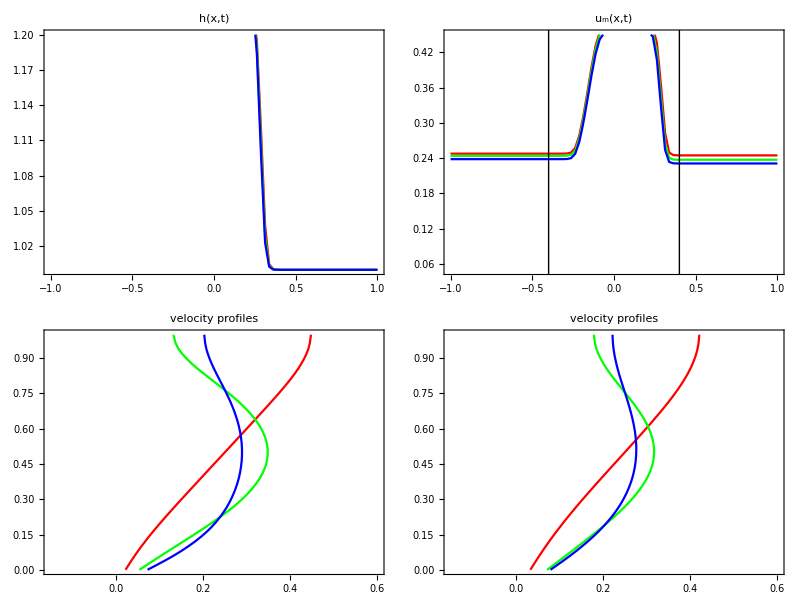

```mathematica
idx={1,2,3,4};

Grid[{{
Plot[Evaluate[Table[hLL[ix][x],{ix,idx}]],{x,x1,x2},
PlotRange->{{x1,x2},{1.0,1.2}},PlotStyle->color⟦1;;Length[idx]⟧,PlotLabel->"h(x,t)",
ImageSize->iSize,Frame->True],
Plot[Evaluate[Table[uMeanLL[ix][x],{ix,idx}]],{x,x1,x2},PlotRange->{{x1,x2},{0.05,0.45}},PlotStyle->color⟦1;;Length[idx]⟧,
PlotLabel->"u_m(x,t)",ImageSize->iSize,
Epilog->{Black,Thin,Line[{{0.4,-10},{0.4,10}}],Line[{{-0.4,-10},{-0.4,10}}]},Frame->True]
},{
ParametricPlot[Evaluate[Table[{uFullLL[ix][-0.4,y],y},{ix,idx}]],{y,y1,y2},AspectRatio->0.5,PlotRange->{{-0.15,0.6},{0,1}},PlotStyle->color⟦1;;Length[idx]⟧,
PlotLabel->"velocity profiles",Frame->True,ImageSize->iSize],
ParametricPlot[Evaluate[Table[{uFullLL[ix][0.4,y],y},{ix,idx}]],{y,y1,y2},AspectRatio->0.5,PlotRange->{{-0.15,0.6},{0,1}},PlotStyle->color⟦1;;Length[idx]⟧,
PlotLabel->"velocity profiles",Frame->True,ImageSize->iSize]
}},
Alignment->{{Right,Left},{Right,Left},{Right,Left}}
]
```